```mathematica
Generator[dist_,recursiondepth_,size_]:=ParallelTable[Median@Nest[Table[RandomVariate[dist]*Abs[#1-#2]+Min[{#1,#2}],2]&@@#&,RandomVariate[dist,2],recursiondepth],size];
Generator1[α_,β_,recursiondepth_,size_]:=ParallelTable[Median@Nest[Table[RandomVariate[BetaDistribution[α,β]]*Abs[#1-#2]+Min[{#1,#2}],2]&@@#&,RandomVariate[BetaDistribution[α,β],2],recursiondepth],size];
Generator2[σ_,recursiondepth_,size_]:=ParallelTable[Median@Nest[Table[RandomVariate[NormalDistribution[0.5,σ]]*Abs[#1-#2]+Min[{#1,#2}],2]&@@#&,RandomVariate[NormalDistribution[0.5,σ],2],recursiondepth],size];
Generator3[recursiondepth_,size_]:=ParallelTable[Median@Nest[Table[RandomVariate[TriangularDistribution[{0,1}]]*Abs[#1-#2]+Min[{#1,#2}],2]&@@#&,RandomVariate[TriangularDistribution[{0,1}],2],recursiondepth],size];
FindParameter[list_]:=FindDistributionParameters[list,BetaDistribution[α,β]];
GraphicParameterFitTest[list_,α_,β_]:=Show[Histogram[list,{0.001},"CDF"],Plot[BetaDistribution[α,β]~CDF~x,{x,0,1}]];
Test[dist_,targetdist_,recursiondepth_,size_,selection_String]:=Module[{list},
	list=Generator[dist,recursiondepth,size];
	Show[Histogram[list,{0.001},selection,PlotLabel->StringJoin["P__ = ",ToString[DistributionFitTest[list,targetdist]]]],
Plot[targetdist~ToExpression[selection]~x,{x,0,1}]]];
IntegratedTest[dist_,recursiondepth_,size_,selection_String]:=Module[{list,targetdist},
targetdist=BetaDistribution[1/(4Variance[dist])-1,1/(4Variance[dist])-1];
	list=Generator[dist,recursiondepth,size];
	Show[Histogram[list,{0.001},selection,PlotLabel->StringJoin["P__ = ",ToString[DistributionFitTest[list,targetdist]]]],
Plot[targetdist~ToExpression[selection]~x,{x,0,1}]]];
```

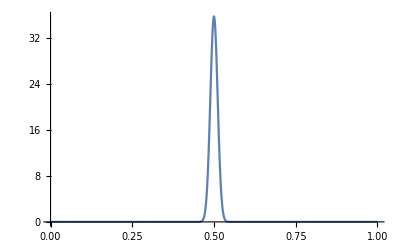

```mathematica
Plot[BetaDistribution[1000,1000]~PDF~x,{x,0,1},PlotRange->All]
```

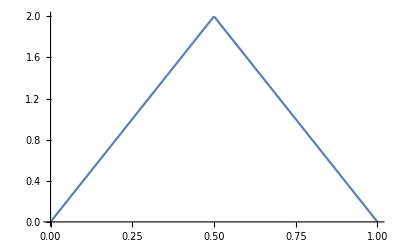

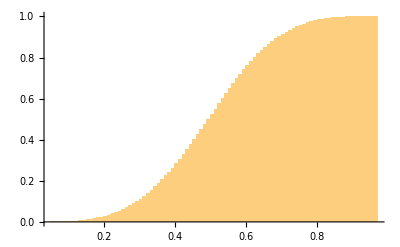

```mathematica
Plot[TriangularDistribution[{0,1}]~PDF~x,{x,0,1},PlotRange->All]
```

```mathematica
FindDistribution[list1=Generator3[100,10000]]
```

WeibullDistribution[3.59564,0.55445]

```mathematica
FindDistribution[list2=Generator2[0.5,100,10000]]
```

LogisticDistribution[0.495652,0.268854]

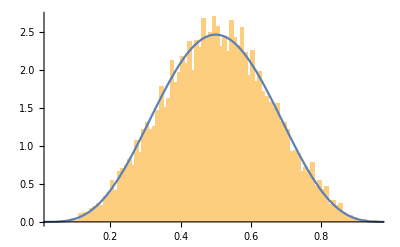

```mathematica
Show[Histogram[list1,{0.01},"PDF"],Plot[BetaDistribution[5,5]~PDF~x,{x,0,1}]]
```

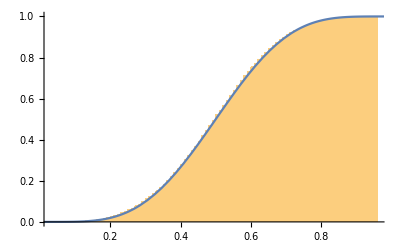

```mathematica
Show[Histogram[list1,{0.01},"CDF"],Plot[BetaDistribution[5,5]~CDF~x,{x,0,1}]]
```

```mathematica
FindDistributionParameters[list1,BetaDistribution[a,b]]
```

{a→4.90325,b→4.86369}

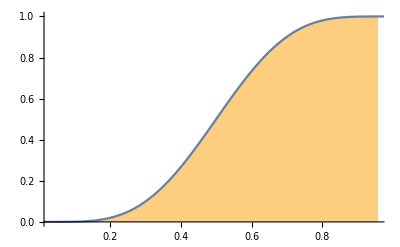

```mathematica
Show[Histogram[list1,{0.001},"CDF"],Plot[BetaDistribution[5,5]~CDF~x,{x,0,1}]]
```

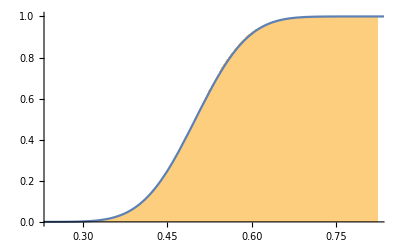

```mathematica
Module[{list3},
list3=Generator2[0.1,100,10000];
GraphicParameterFitTest[list3,23.5,23.5]]
```

```mathematica
FindDistributionParameters[list1,NormalDistribution[0.5,σ]]
```

{σ→0.151977}

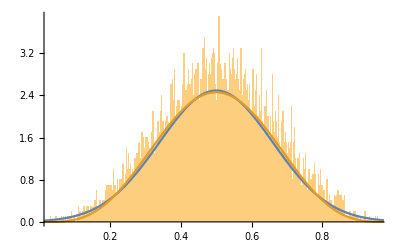

```mathematica
Show[Histogram[list1,{0.001},"PDF"],Plot[{NormalDistribution[0.5,0.16]~PDF~x,BetaDistribution[5,5]~PDF~x},{x,0,1}]]
```

```mathematica
DistributionFitTest[list1,BetaDistribution[5,5]]
```

0.169268

```mathematica
DistributionFitTest[list1,NormalDistribution[0.5,0.16]]
```

0.0909936

```mathematica
Variance[BetaDistribution[a,a]]
```

1/(4 (1+2 a))

```mathematica
Variance[list1]
```

0.023095

```mathematica
Variance[BetaDistribution[5,5]]//N
```

0.0227273

```mathematica
TriangularDistribution[{0,1}]//Variance//N
```

0.0416667

```mathematica
Variance[BetaDistribution[2.5,2.5]]//N
```

0.0416667

```mathematica
Solve[1/(4(1+2a))==x,a]//Expand
```

{{a→-1/2+1/(8 x)}}

```mathematica
Solve[1/(4(1+2a))==Variance[TriangularDistribution[{0,1}]],a]
```

{{a→5/2}}

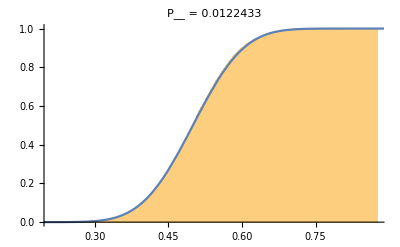

```mathematica
IntegratedTest[StudentTDistribution[0.5,0.1,10],100,10000,"CDF"]
```

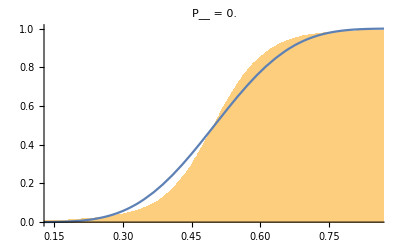

```mathematica
IntegratedTest[StudentTDistribution[0.5,0.1,3],100,10000,"CDF"]
```

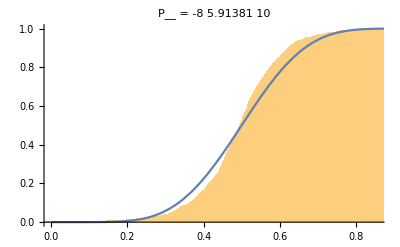

```mathematica
IntegratedTest[StudentTDistribution[0.5,0.1,3],1000,1000,"CDF"]
```

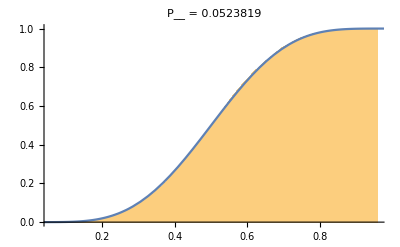

```mathematica
IntegratedTest[TriangularDistribution[{0,1}],100,10000,"CDF"]
```

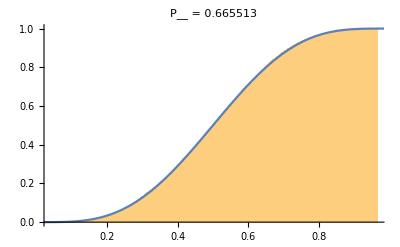

```mathematica
IntegratedTest[BetaDistribution[2,2],100,10000,"CDF"]
```

```mathematica
TransformedDistribution[(a+b+c)/3,{a,b,c}\[Distributed]BernoulliDistribution[0.5]]
```

TransformedDistribution[1/3 (x1+x2+x3),{x1,x2,x3}\[Distributed]BernoulliDistribution[0.5]]

```mathematica
IntegratedTest[TransformedDistribution[(a+b+c)/3,{a,b,c}\[Distributed]BernoulliDistribution[0.5]],100,10000,"CDF"]
```

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{Min[2,TransformedDistribution[1/3 (x1+x2+x3),{x1,x2,x3}\[Distributed]BernoulliDistribution[0.5]]]+Abs[-2+TransformedDistribution[Times[«2»],Distributed[«2»]]] RandomVariate[TransformedDistribution[1/3 Plus[«3»],{«3»}\[Distributed]BernoulliDistribution[«1»]]],Min[2,TransformedDistribution[1/3 (x1+x2+x3),{x1,x2,x3}\[Distributed]«21»[0.5]]]+Abs[«1»] «1»}].

General::stop: Further output of Median::rectn will be suppressed during this calculation.

$Aborted

```mathematica
TransformedDistribution[(a+b+c)/3,{a,b,c}\[Distributed]BernoulliDistribution[0.5]]~CDF~x
```

CDF[TransformedDistribution[1/3 (x1+x2+x3),{x1,x2,x3}\[Distributed]BernoulliDistribution[0.5]],x]

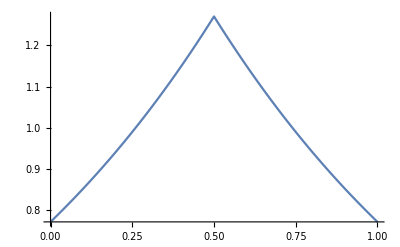

```mathematica
Plot[PDF[ProbabilityDistribution[E^(-Abs[x-1/2])/#,{x,0,1}]][x],{x,0,1}]&[Integrate[E^(-Abs[x-1/2]),{x,0,1}]]
```

```mathematica
Integrate[PDF[ProbabilityDistribution[E^(-Abs[x-1/2]),{x,0,1}]][x],{x,0,1}]//N
```

0.786939

```mathematica
ProbabilityDistribution[E^(-Abs[x-1/2])/Integrate[E^(-Abs[x-1/2]),{x,0,1}],{x,0,1}]
```

ProbabilityDistribution[ⅇ^(1/2-Abs[-1/2+x])/(2 (-1+√ⅇ)),{x,0,1}]

```mathematica
IntegratedTest[ProbabilityDistribution[E^(-Abs[x-1/2])/Integrate[E^(-Abs[x-1/2]),{x,0,1}],{x,0,1}],100,1000,"CDF"]
```

$Aborted

```mathematica
ProbabilityDistribution[E^(-Abs[x-1/2])/Integrate[E^(-Abs[x-1/2]),{x,0,1}],{x,0,1}]
```

ProbabilityDistribution[ⅇ^(1/2-Abs[-1/2+x])/(2 (-1+√ⅇ)),{x,0,1}]

```mathematica
Variance[ProbabilityDistribution[E^(-Abs[x-1/2])/Integrate[E^(-Abs[x-1/2]),{x,0,1}],{x,0,1}]]
```

(-13+8 √ⅇ)/(4 (-1+√ⅇ))

```mathematica
list1=Generator[ProbabilityDistribution[E^(-Abs[x-1/2])/Integrate[E^(-Abs[x-1/2]),{x,0,1}],{x,0,1}],100,10000]//AbsoluteTiming
```

{10329.1,{0.385987,0.454456,0.774567,0.393397,0.273496,0.755367,0.481957,9987,0.500189,0.378666,0.837899,0.428188,0.0947206,0.75458}}
 |  |  |  |

```mathematica
Needs["CUDALink`"]
```

```mathematica
CUDAInformation[]
```

{1→{Name→GeForce GTX 1080,Clock Rate→1835000,Compute Capabilities→6.1,GPU Overlap→1,Maximum Block Dimensions→{1024,1024,64},Maximum Grid Dimensions→{2147483647,65535,65535},Maximum Threads Per Block→1024,Maximum Shared Memory Per Block→49152,Total Constant Memory→65536,Warp Size→32,Maximum Pitch→2147483647,Maximum Registers Per Block→65536,Texture Alignment→512,Multiprocessor Count→20,Core Count→640,Execution Timeout→1,Integrated→False,Can Map Host Memory→True,Compute Mode→Default,Texture1D Width→131072,Texture2D Width→131072,Texture2D Height→65536,Texture3D Width→16384,Texture3D Height→16384,Texture3D Depth→16384,Texture2D Array Width→32768,Texture2D Array Height→32768,Texture2D Array Slices→2048,Surface Alignment→512,Concurrent Kernels→True,ECC Enabled→False,TCC Enabled→False,Total Memory→8589934592}}

```mathematica
CUDAQ[]
```

True

```mathematica
ParallelTable[i^3,{i,1,10,1}]
```

{1,8,27,64,125,216,343,512,729,1000}

```mathematica
list3=Table[If[RandomReal[]≥0.5,0.5,If[RandomReal[]≥0.5,1,0]],100000];
```

```mathematica
FindDistribution[list3]
```

MixtureDistribution[{0.278146,0.278146,0.443709},{NormalDistribution[0.0011266,0.0551736],NormalDistribution[0.987167,0.0572159],NormalDistribution[0.494481,0.0574879]}]

$Aborted

Part::partd: Part specification list1⟦2⟧ is longer than depth of object.

Histogram::ldata: list1⟦2⟧ is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[list1⟦2⟧,{0.001},CDF],].

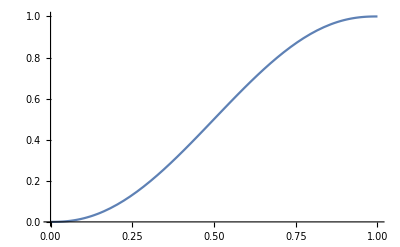
Show[Histogram[list1⟦2⟧,{0.001},CDF],-Graphics-]

```mathematica
Show[Histogram[list1[[2]],{0.001},"CDF"],Plot[BetaDistribution[1/(4#)-1&[(-13+8 √ⅇ)/(4 (-1+√ⅇ))],1/(4#) -1&[(-13+8 √ⅇ)/(4 (-1+√ⅇ))]]~CDF~x,{x,0,1}]]
```

```mathematica
list1[[2]]
```

{0.385987,0.454456,0.774567,0.393397,0.273496,0.755367,0.481957,0.523032,0.535923,0.230194,0.769727,0.146669,0.714128,0.645943,0.258154,0.629185,0.139936,0.557706,0.65895,0.327127,0.468274,0.435322,0.656849,0.570492,0.79113,0.514272,0.0256932,0.481996,0.425897,0.547094,0.772051,0.658347,0.439941,0.270643,0.684134,0.30594,0.44377,0.311979,0.535777,0.731136,0.259805,0.43409,0.558806,0.510318,0.651807,0.0282276,0.864428,0.452408,0.150381,0.721964,0.843909,0.589147,0.711336,0.849709,0.876723,0.410812,0.573499,0.591708,0.424335,0.543969,0.450315,0.6049,0.280627,0.53251,0.452495,0.859519,0.699682,0.336802,0.54977,0.458194,0.37298,0.767395,0.194023,0.164329,0.203546,0.660388,0.649947,0.748032,0.585976,0.79652,0.588061,0.527516,0.483033,0.727861,0.210879,0.638506,0.646565,0.596432,0.407327,0.505884,0.326137,0.430859,0.362265,0.358542,0.345828,0.74495,0.202774,0.638872,0.605471,0.880525,0.497909,0.660762,0.477747,0.716401,0.489051,0.150766,0.861665,0.802869,0.778586,0.352628,0.352481,0.824609,0.445605,0.847842,0.0920606,0.352215,0.222083,0.389287,0.29677,0.472063,0.451235,0.736672,0.475098,0.361663,0.690917,0.429555,0.335631,0.624173,0.237646,0.576056,0.224991,0.90328,0.740695,0.317906,0.804342,0.501915,0.834234,0.276277,0.342949,0.647954,0.622445,0.751284,0.271965,0.5247,0.597323,0.574301,0.310064,0.824597,0.554103,0.511695,0.109439,0.866158,0.56808,0.684145,0.214902,0.77985,0.777411,0.289357,0.418035,0.274056,0.240188,0.479091,0.618409,0.501351,0.447158,0.530683,0.480865,0.37775,0.419187,0.708364,0.161616,0.353098,0.376742,0.521626,0.765576,0.638089,0.476903,0.554709,0.471875,0.886742,0.678932,0.58324,0.741229,0.558558,0.41878,0.510474,0.354852,0.789754,0.372081,0.797152,0.5334,0.272599,0.597088,0.755654,0.506701,0.753966,0.404211,0.727408,0.378307,0.935214,0.347501,0.474731,0.501345,0.155178,0.116311,0.658055,0.468703,0.231553,0.949394,0.725025,0.639128,0.589533,0.607287,0.691559,0.299774,0.28072,0.877412,0.284165,0.554996,0.541286,0.261754,0.326649,0.459786,0.355181,0.385121,0.656423,0.23439,0.326876,0.792825,0.562928,0.622784,0.318493,0.420153,0.385238,0.203826,0.709079,0.348882,0.694043,0.502909,0.454502,0.514619,0.576217,0.41007,0.368634,0.4087,0.332149,0.4734,0.271531,0.545237,0.837945,0.794453,0.903919,0.540599,0.208373,0.261218,0.262024,0.670828,0.723892,0.647361,0.695767,0.415808,0.767166,0.607113,0.328025,0.518802,0.663016,0.333811,0.671158,0.451105,0.847677,0.282827,0.517685,0.315699,0.647153,0.311464,0.771676,0.298411,0.365566,0.284539,0.28615,0.692985,0.767996,0.688299,0.671915,0.757123,0.408636,0.851404,0.262796,0.497772,0.795543,0.535205,0.531252,0.506615,0.475433,0.510084,0.767811,0.94914,0.692064,0.696289,0.448305,0.36994,0.355341,0.744443,0.744147,0.492869,0.796492,0.441438,0.439013,0.407407,0.227919,0.722674,0.954608,0.651529,0.371334,0.336573,0.416453,0.373203,0.300009,0.533566,0.402572,0.277549,0.552805,0.716331,0.567453,0.653759,0.481483,0.435936,0.169694,0.301707,0.516198,0.687923,0.596069,0.562155,0.579228,0.736843,0.540818,0.193874,0.539006,0.255893,0.230239,0.289995,0.336155,0.313383,0.368847,0.790508,0.0594851,0.448509,0.202843,0.433341,0.573508,0.112952,0.338737,0.301064,0.136502,0.672384,0.584566,0.29821,0.147671,0.591457,0.386735,0.607886,0.891111,0.332132,0.887749,0.312011,0.346449,0.862973,0.396475,0.284162,0.0150182,0.261949,0.847617,0.427947,0.75949,0.400357,0.827525,0.537451,0.114604,0.485634,0.705082,0.568468,0.620484,0.807729,0.711447,0.41899,0.560131,0.251464,0.676454,0.411062,0.388079,0.320291,0.126974,0.0884339,0.152227,0.697226,0.465432,0.521089,0.533018,0.436746,0.793475,0.584275,0.51405,0.384561,0.424196,0.297167,0.439417,0.516665,0.764468,0.608086,0.50731,0.268049,0.506768,0.243085,0.561884,0.0907088,0.479059,0.431892,0.776418,0.374306,0.708264,0.264284,0.528534,0.747341,0.644531,0.502417,0.65589,0.607206,0.372992,0.225901,0.369363,0.149315,0.776392,0.0494209,0.35536,0.415935,0.516326,0.446583,0.414351,0.509691,0.832156,0.718748,0.836631,0.485642,0.529761,0.825052,0.689828,0.0799442,0.792637,0.184804,0.688744,0.321989,0.383985,0.901275,0.10497,0.736583,0.335453,0.545675,0.284179,0.485091,0.379692,0.874642,0.678951,0.983485,0.610341,0.145388,0.179048,0.585233,0.662431,0.74619,0.158066,0.835889,0.894242,0.649543,0.501301,0.635429,0.44443,0.339129,0.537811,0.67032,0.55323,0.11682,0.0848903,0.519125,0.58212,0.716256,0.2377,0.750834,0.484167,0.321754,0.483984,0.89116,0.271895,0.392873,0.30791,0.134363,0.512707,0.845243,0.139376,0.786777,0.647887,0.490962,0.519863,0.455065,0.303667,0.510774,0.247243,0.270146,0.477372,0.378252,0.43813,0.162848,0.393144,0.870652,0.528678,0.607075,0.823561,0.706863,0.847639,0.318386,0.159993,0.626708,0.80827,0.468618,0.271937,0.588033,0.63008,0.826204,0.410832,0.279586,0.35799,0.433881,0.905962,0.185504,0.8168,0.177446,0.230905,0.428279,0.227643,0.541711,0.728348,0.25709,0.452107,0.298762,0.630912,0.299387,0.415373,0.288922,0.884468,0.308352,0.533759,0.343973,0.731851,0.720577,0.364651,0.607399,0.306602,0.352531,0.334028,0.598454,0.398537,0.233983,0.599136,0.836751,0.502424,0.4051,0.447106,0.231395,0.556143,0.377044,0.593776,0.413839,0.311499,0.517846,0.367529,0.615745,0.794296,0.294758,0.774726,0.825563,0.394102,0.412907,0.50075,0.645996,0.746902,0.344206,0.453026,0.335322,0.541294,0.13809,0.600816,0.843108,0.44103,0.444177,0.444263,0.600318,0.438721,0.733791,0.452925,0.593043,0.43247,0.751152,0.312828,0.660483,0.629701,0.610225,0.452321,0.867748,0.821393,0.32518,0.536265,0.456796,0.243479,0.51424,0.464696,0.181622,0.346358,0.109171,0.126444,0.40936,0.832442,0.643533,0.261312,0.18188,0.560434,0.148753,0.740984,0.559008,0.529187,0.511248,0.639081,0.281038,0.579867,0.566561,0.270218,0.577878,0.444783,0.444119,0.109118,0.673853,0.213047,0.6294,0.569244,0.509421,0.41128,0.486919,0.326504,0.706805,0.627548,0.914999,0.161276,0.50814,0.535684,0.335209,0.616106,0.263391,0.132769,0.576478,0.513346,0.403944,0.774681,0.470333,0.604313,0.672715,0.522354,0.754942,0.655808,0.615658,0.422381,0.145881,0.589489,0.0636449,0.723226,0.535167,0.554753,0.407061,0.201618,0.871548,0.799439,0.65567,0.381479,0.450949,0.458042,0.284798,0.214663,0.213822,0.600388,0.331784,0.650611,0.265082,0.516898,0.695477,0.637131,0.534098,0.436806,0.646052,0.710482,0.28095,0.425961,0.420718,0.742643,0.715259,0.14069,0.796416,0.463754,0.0799462,0.344689,0.862976,0.145013,0.601373,0.183912,0.420573,0.723513,0.839087,0.13092,0.546261,0.818371,0.835899,0.257287,0.387557,0.250552,0.672563,0.767604,0.816818,0.442209,0.227066,0.679049,0.378977,0.410493,0.353643,0.72078,0.52868,0.521702,0.372656,0.352363,0.552979,0.71139,0.723192,0.799716,0.700488,0.507171,0.593249,0.586562,0.71812,0.227605,0.295687,0.542454,0.686916,0.526886,0.0788701,0.431627,0.217867,0.389491,0.531517,0.33543,0.569249,0.186058,0.562806,0.747051,0.693864,0.163114,0.605503,0.661474,0.723121,0.406657,0.438452,0.330364,0.684261,0.594602,0.399401,0.590868,0.748369,0.41055,0.526449,0.209291,0.510101,0.506244,0.758058,0.241338,0.468343,0.324011,0.620475,0.315823,0.351759,0.571354,0.681193,0.596223,0.55376,0.564594,0.233899,0.464085,0.189409,0.474135,0.576489,0.551396,0.286862,0.142971,0.432367,0.381541,0.83814,0.595275,0.283842,0.445409,0.29844,0.299683,0.498191,0.516688,0.234568,0.962935,0.610244,0.213449,0.684929,0.41413,0.410106,0.574945,0.408096,0.704913,0.550627,0.234075,0.317119,0.487424,0.378976,0.302814,0.701843,0.388443,0.548472,0.27779,0.795992,0.528924,0.383843,0.515701,0.52615,0.422022,0.630353,0.508336,0.411639,0.869344,0.710295,0.254086,0.193498,0.772311,0.293314,0.697278,0.708203,0.176867,0.420653,0.481792,0.360992,0.315929,0.53676,0.3821,0.947988,0.291702,0.761348,0.637094,0.517735,0.758586,0.309265,0.0923572,0.318208,0.598247,0.46672,0.487973,0.562313,0.765299,0.358738,0.265406,0.305704,0.447252,0.417411,0.783041,0.6067,0.20323,0.397181,0.439386,0.337834,0.696719,0.776295,0.767568,0.543008,0.333571,0.219932,0.617565,0.520001,0.562041,0.286127,0.778611,0.399985,0.240863,0.484709,0.381705,0.457743,0.552521,0.309813,0.0972665,0.18813,0.326543,0.405232,0.347152,0.312763,0.326758,0.72831,0.12947,0.931903,0.685502,0.331666,0.678277,0.314882,0.313489,0.0295717,0.490722,0.264673,0.308784,0.636833,0.578674,0.496806,0.209982,0.50491,0.647052,0.703547,0.513298,0.388941,0.42671,0.722537,0.948705,0.458966,0.194922,0.910273,0.583504,0.557417,0.866804,0.406107,0.454064,0.660779,0.619474,0.457264,0.220259,0.636177,0.712805,0.445363,0.54717,0.40931,0.606572,0.337725,0.410732,0.771822,0.664284,0.726159,0.585943,0.542999,0.292633,0.75767,0.510804,0.736401,0.43001,0.743439,0.557285,0.31106,0.588477,0.425237,0.842795,0.597806,0.263399,0.328375,0.346077,0.790658,0.341035,0.418297,0.637625,0.91155,0.436736,0.568352,0.654628,0.914893,0.203305,0.743411,0.395282,0.484687,0.344533,0.812085,0.0665299,0.514609,0.850296,0.27561,0.551123,0.387797,0.262145,0.500779,0.667408,0.118335,0.419428,0.914512,0.256607,0.520561,0.421558,0.58127,0.513669,0.514848,0.227269,0.731136,0.484192,0.705333,0.139283,0.323996,0.602699,0.667656,0.0138949,0.864834,0.720595,0.626729,0.180523,0.693691,0.400203,0.84861,0.74018,0.725658,0.773506,0.545809,0.431722,0.94473,0.677988,0.406407,0.170774,0.535644,0.245625,0.29083,0.276909,0.655408,0.645868,0.724602,0.495062,0.582931,0.601469,0.598949,0.736083,0.447357,0.525277,0.526772,0.700429,0.369388,0.597064,0.34339,0.541221,0.29777,0.567368,0.587196,0.688881,0.36539,0.653476,0.417944,0.193503,0.412078,0.353613,0.595572,0.874471,0.471018,0.75567,0.255313,0.346503,0.483901,0.152741,0.686806,0.407691,0.576972,0.287182,0.11116,0.521418,0.411111,0.685828,0.567176,0.438442,0.821588,0.318435,0.679462,0.149223,0.721614,0.328316,0.54499,0.577193,0.542546,0.490884,0.274146,0.527434,0.450212,0.322296,0.448788,0.555373,0.441531,0.303409,0.430679,0.527112,0.528825,0.340606,0.517415,0.430554,0.617548,0.147357,0.361089,0.608164,0.230797,0.494094,0.559336,0.3097,0.176383,0.469952,0.682977,0.754037,0.518891,0.230867,0.450269,0.80566,0.587989,0.743509,0.608254,0.733107,0.58836,0.616696,0.439341,0.497661,0.661867,0.586722,0.46108,0.712845,0.0804476,0.844974,0.573822,0.878775,0.679848,0.743821,0.493247,0.314531,0.414617,0.899493,0.496519,0.8612,0.824229,0.453996,0.448682,0.617446,0.16895,0.599105,0.147594,0.448847,0.541919,0.505441,0.596173,0.160184,0.447999,0.207232,0.509885,0.304497,0.882673,0.816982,0.775607,0.105823,0.123088,0.30114,0.863584,0.833918,0.293927,0.646788,0.479473,0.563411,0.72721,0.59452,0.594857,0.616633,0.416277,0.290104,0.8084,0.39554,0.8343,0.25883,0.75769,0.64483,0.495775,0.293618,0.33336,0.695903,0.166052,0.578772,0.721226,0.774329,0.434199,0.560855,0.705871,0.231172,0.699938,0.32481,0.396076,0.667877,0.524238,0.327799,0.521083,0.692936,0.439939,0.381488,0.538296,0.432814,0.755618,0.592696,0.446572,0.563863,0.560791,0.5992,0.273193,0.503847,0.202528,0.121578,0.35544,0.121804,0.262705,0.116865,0.945524,0.491805,0.45183,0.768483,0.661749,0.265028,0.9574,0.51995,0.353186,0.758541,0.491957,0.293877,0.365127,0.471773,0.568431,0.819358,0.780331,0.499894,0.766674,0.297888,0.344143,0.332531,0.749027,0.228534,0.507248,0.524565,0.748456,0.855237,0.186436,0.363295,0.552432,0.583219,0.592774,0.619242,0.402323,0.84767,0.507138,0.321116,0.697319,0.428289,0.520338,0.492329,0.339579,0.611307,0.556243,0.821125,0.453965,0.553236,0.587072,0.261663,0.739531,0.762835,0.410816,0.377923,0.867246,0.199345,0.876832,0.459899,0.635197,0.54396,0.51821,0.443006,0.414215,0.60779,0.568204,0.285984,0.253582,0.451328,0.0949921,0.143734,0.552235,0.611412,0.114086,0.358721,0.582819,0.562143,0.761359,0.323558,0.801976,0.737056,0.437824,0.465652,0.262626,0.222795,0.788511,0.496108,0.500844,0.807054,0.200583,0.188846,0.649487,0.364292,0.527439,0.44094,0.445973,0.822124,0.261921,0.307261,0.679661,0.740994,0.432364,0.493554,0.260592,0.264071,0.418568,0.765748,0.717488,0.655096,0.242784,0.32305,0.449438,0.500214,0.363783,0.557827,0.413833,0.796367,0.509252,0.379715,0.686622,0.903282,0.250132,0.279364,0.727979,0.238325,0.388284,0.434141,0.287043,0.476905,0.353341,0.571186,0.777431,0.549951,0.838379,0.346475,0.346687,0.550362,0.397274,0.708464,0.672321,0.767581,0.412275,0.902958,0.328157,0.26618,0.508187,0.630298,0.741246,0.177058,0.15191,0.89797,0.599447,0.582517,0.455294,0.408044,0.289153,0.353433,0.678518,0.358884,0.807943,0.730389,0.732342,0.368681,0.638585,0.446465,0.51867,0.370884,0.576933,0.75896,0.47204,0.260239,0.138974,0.70847,0.836049,0.45099,0.49525,0.563533,0.605553,0.382498,0.35144,0.438867,0.343586,0.473952,0.500179,0.266111,0.106661,0.0555186,0.446876,0.75329,0.471644,0.403359,0.203609,0.286326,0.443728,0.884994,0.745311,0.238141,0.484971,0.101453,0.450475,0.802129,0.118261,0.554821,0.231495,0.423014,0.341958,0.65414,0.881379,0.355501,0.363326,0.728728,0.108892,0.263006,0.815731,0.73814,0.703036,0.518653,0.225407,0.0919446,0.132695,0.68009,0.534625,0.445997,0.377491,0.637347,0.195999,0.522791,0.299671,0.608115,0.560599,0.954461,0.636069,0.445512,0.0843077,0.259623,0.348414,0.849836,0.219648,0.879997,0.622294,0.480271,0.856325,0.627831,0.270378,0.342047,0.214253,0.660018,0.306782,0.898263,0.216552,0.511899,0.641604,0.146783,0.225424,0.562266,0.601902,0.777767,0.503474,0.236526,0.196016,0.309275,0.879794,0.496535,0.35026,0.118067,0.597552,0.281011,0.543356,0.409159,0.315104,0.013827,0.334051,0.279397,0.665196,0.500946,0.836667,0.576147,0.499147,0.413245,0.534973,0.78176,0.659049,0.332676,0.450049,0.102898,0.6038,0.529733,0.51512,0.82349,0.33566,0.489832,0.68176,0.691353,0.627029,0.472788,0.725644,0.230421,0.454031,0.530548,0.769648,0.376985,0.246733,0.764926,0.742596,0.659231,0.332632,0.127647,0.683142,0.68482,0.506131,0.239174,0.229447,0.765111,0.754537,0.583603,0.261273,0.857746,0.566658,0.409381,0.467619,0.361766,0.652025,0.695552,0.518122,0.168153,0.640559,0.64854,0.61032,0.766031,0.711334,0.161239,0.381312,0.635543,0.742017,0.454835,0.404532,0.48951,0.740114,0.820914,0.384649,0.622573,0.605294,0.774663,0.677498,0.466632,0.752193,0.339671,0.418328,0.435419,0.69991,0.204693,0.49871,0.378837,0.548476,0.604446,0.467663,0.307049,0.318703,0.405424,0.762473,0.454565,0.642132,0.456748,0.300218,0.102544,0.601682,0.163584,0.644919,0.24508,0.689311,0.415475,0.78586,0.34211,0.299637,0.530366,0.420742,0.367538,0.682395,0.384845,0.555726,0.336052,0.714393,0.312846,0.52476,0.0984997,0.718741,0.87207,0.182114,0.569225,0.80281,0.842805,0.673329,0.664932,0.700675,0.659546,0.478861,0.659263,0.931161,0.383151,0.610875,0.483096,0.438539,0.701279,0.572672,0.436094,0.314385,0.393315,0.673575,0.825254,0.808073,0.333428,0.63206,0.324901,0.373576,0.75256,0.400648,0.375686,0.635364,0.537308,0.436456,0.863615,0.583508,0.588708,0.601143,0.655415,0.293089,0.307407,0.787728,0.171766,0.73493,0.438934,0.284373,0.678049,0.33827,0.493554,0.400337,0.608749,0.618113,0.722102,0.356712,0.596555,0.53907,0.590029,0.141791,0.670847,0.411717,0.83905,0.401301,0.674581,0.62724,0.211864,0.767668,0.694949,0.719419,0.144804,0.613577,0.643841,0.661383,0.509664,0.48587,0.282979,0.118321,0.599059,0.410178,0.650245,0.49723,0.162685,0.42239,0.256789,0.239773,0.726157,0.43677,0.844898,0.779953,0.422348,0.389945,0.0148929,0.082557,0.807915,0.298736,0.847346,0.287098,0.914069,0.510285,0.355123,0.260651,0.444746,0.15458,0.551348,0.148337,0.371718,0.332663,0.560475,0.379437,0.0421985,0.870503,0.506477,0.440567,0.214316,0.475839,0.568407,0.733601,0.489386,0.249123,0.720217,0.272958,0.640741,0.498836,0.446734,0.0920602,0.409052,0.512337,0.578046,0.630203,0.761931,0.307215,0.780545,0.61427,0.893503,0.537426,0.520922,0.830087,0.380894,0.384611,0.401214,0.399052,0.363663,0.577307,0.439832,0.472651,0.208106,0.36589,0.223061,0.59316,0.198399,0.794296,0.578564,0.347037,0.522494,0.25968,0.742673,0.568855,0.605667,0.314571,0.229468,0.69727,0.780974,0.809753,0.239612,0.37444,0.507473,0.418698,0.720713,0.14547,0.872318,0.714171,0.304258,0.242363,0.799324,0.565251,0.827939,0.565314,0.817538,0.320594,0.499773,0.235184,0.258561,0.259239,0.310359,0.584967,0.496166,0.411211,0.871036,0.771675,0.530957,0.336218,0.576097,0.290359,0.708249,0.872101,0.151183,0.626933,0.504963,0.25236,0.644878,0.427967,0.364925,0.331498,0.744628,0.522554,0.460177,0.670747,0.369069,0.732813,0.16275,0.616688,0.463814,0.578205,0.368254,0.680053,0.719531,0.618315,0.769811,0.276788,0.652318,0.802871,0.546637,0.495514,0.80033,0.325796,0.747435,0.617235,0.454422,0.695106,0.76353,0.443148,0.495888,0.22941,0.484478,0.851094,0.584941,0.48174,0.517945,0.354789,0.358453,0.395928,0.564834,0.540972,0.393757,0.0607767,0.474203,0.310751,0.673369,0.194333,0.631436,0.825748,0.431569,0.739815,0.249238,0.526576,0.403139,0.539119,0.871439,0.105134,0.694947,0.460173,0.944229,0.265097,0.499058,0.498578,0.415499,0.808592,0.596518,0.623523,0.512631,0.551557,0.618066,0.622303,0.780985,0.478227,0.490139,0.649331,0.320439,0.411947,0.907428,0.622241,0.443406,0.329391,0.605162,0.317466,0.391475,0.839461,0.655096,0.73722,0.476445,0.0479153,0.707325,0.790782,0.191589,0.550676,0.633068,0.705099,0.104764,0.702147,0.482777,0.389089,0.641946,0.66568,0.751104,0.354096,0.245659,0.767284,0.29085,0.412992,0.290985,0.469933,0.193699,0.119972,0.413088,0.103629,0.439191,0.478089,0.525069,0.325639,0.713567,0.469233,0.814706,0.0487622,0.526914,0.690773,0.396544,0.617895,0.34324,0.84108,0.781882,0.502592,0.358366,0.608301,0.692549,0.503902,0.66546,0.451858,0.260472,0.631031,0.64063,0.332029,0.338276,0.66887,0.561609,0.347247,0.772621,0.62752,0.0716581,0.407361,0.738263,0.481959,0.658658,0.358267,0.595027,0.401164,0.456961,0.42275,0.31326,0.144367,0.517961,0.465979,0.641369,0.352032,0.663548,0.866862,0.442365,0.173639,0.434864,0.518171,0.331914,0.623816,0.357569,0.409789,0.37444,0.674785,0.898779,0.666708,0.601124,0.551694,0.9012,0.585283,0.512305,0.236325,0.512631,0.783885,0.436008,0.363959,0.200619,0.665628,0.539232,0.378587,0.855383,0.463094,0.757267,0.780596,0.392198,0.480717,0.365914,0.400428,0.962906,0.576259,0.143383,0.417904,0.351706,0.838425,0.808683,0.36629,0.393871,0.355062,0.822355,0.82432,0.227454,0.479972,0.678296,0.357347,0.378467,0.174963,0.248034,0.470592,0.500753,0.738039,0.600965,0.425918,0.250188,0.65934,0.633813,0.384495,0.495939,0.920063,0.475438,0.635527,0.364014,0.667595,0.801242,0.613942,0.311486,0.177436,0.519302,0.549596,0.276655,0.794857,0.73591,0.772615,0.604744,0.225335,0.370087,0.232807,0.437763,0.662578,0.436785,0.791391,0.291576,0.598137,0.567505,0.429053,0.259064,0.297375,0.424113,0.798571,0.252254,0.440677,0.311314,0.845365,0.642664,0.760833,0.27213,0.517668,0.717762,0.331933,0.681497,0.589255,0.736956,0.614866,0.314258,0.206098,0.642971,0.704537,0.542126,0.614415,0.515628,0.507675,0.332083,0.614831,0.342066,0.457098,0.82877,0.500617,0.413067,0.389091,0.380206,0.635004,0.492843,0.651792,0.58858,0.383499,0.375055,0.357558,0.472867,0.877055,0.798849,0.345034,0.579661,0.837739,0.331866,0.415855,0.555643,0.826221,0.844653,0.313445,0.774246,0.0260871,0.229954,0.493788,0.94474,0.655052,0.689072,0.649189,0.0728577,0.487261,0.575172,0.225261,0.645597,0.333916,0.258589,0.935979,0.447465,0.645284,0.591325,0.473868,0.318621,0.726307,0.762956,0.396795,0.638298,0.592319,0.791876,0.556082,0.290722,0.339851,0.431887,0.21338,0.302498,0.66695,0.328892,0.748295,0.72208,0.233655,0.582317,0.582703,0.714115,0.463984,0.60287,0.254712,0.732122,0.747432,0.306903,0.402497,0.251803,0.310999,0.431105,0.56049,0.599983,0.598838,0.24858,0.588082,0.515123,0.178102,0.546282,0.621127,0.429911,0.503405,0.426753,0.33877,0.310272,0.199539,0.44434,0.54835,0.317637,0.742755,0.568732,0.394834,0.407739,0.578975,0.527949,0.717901,0.448606,0.62159,0.595741,0.476044,0.796859,0.191377,0.795997,0.694516,0.673336,0.594299,0.803528,0.370739,0.740125,0.39723,0.363142,0.588015,0.719341,0.677241,0.769886,0.61352,0.629024,0.341839,0.720459,0.547318,0.338987,0.442031,0.664374,0.348861,0.371667,0.382533,0.675207,0.504545,0.820735,0.344438,0.5383,0.613633,0.12147,0.354069,0.469189,0.867194,0.727139,0.396319,0.852453,0.482751,0.468658,0.477203,0.418097,0.0788851,0.255337,0.7026,0.413121,0.611427,0.232272,0.548056,0.253209,0.748987,0.32093,0.456634,0.825185,0.775079,0.116539,0.571342,0.552595,0.401491,0.128647,0.446284,0.836417,0.922508,0.379965,0.773544,0.605059,0.496788,0.584179,0.120402,0.598793,0.297309,0.457306,0.66559,0.643017,0.240802,0.187978,0.256626,0.695485,0.798323,0.686535,0.848755,0.470134,0.307395,0.846832,0.191877,0.654948,0.444259,0.377268,0.22819,0.443947,0.691325,0.504596,0.544029,0.848743,0.290183,0.336789,0.508617,0.844528,0.344113,0.704821,0.298004,0.611458,0.450382,0.318947,0.403219,0.417341,0.392604,0.226438,0.706759,0.573434,0.561781,0.454661,0.0551564,0.650847,0.589478,0.70027,0.435073,0.343811,0.220913,0.284918,0.489118,0.498556,0.195137,0.134049,0.266265,0.49403,0.20891,0.7503,0.114862,0.381419,0.460846,0.750992,0.579421,0.59004,0.556301,0.237381,0.301213,0.636848,0.607255,0.687168,0.30463,0.644578,0.35607,0.603053,0.349968,0.325339,0.659747,0.61528,0.731654,0.200665,0.724198,0.442907,0.873616,0.437901,0.592292,0.298282,0.814513,0.837568,0.361022,0.836995,0.47475,0.623824,0.278178,0.959481,0.624118,0.203995,0.214853,0.188719,0.435234,0.683874,0.584008,0.611316,0.578092,0.234146,0.527012,0.215801,0.65811,0.701745,0.491958,0.132329,0.452477,0.782198,0.314175,0.812447,0.435656,0.561469,0.196394,0.333273,0.221259,0.648032,0.628439,0.813016,0.466999,0.347673,0.346037,0.446702,0.32443,0.178484,0.574623,0.443978,0.524067,0.822405,0.415834,0.487343,0.506798,0.70554,0.441328,0.532037,0.767353,0.371965,0.572193,0.561335,0.324316,0.427411,0.360863,0.33221,0.171679,0.173505,0.365561,0.312865,0.536696,0.659305,0.519849,0.693327,0.75291,0.149952,0.713099,0.49056,0.390321,0.659708,0.924508,0.27323,0.428977,0.773893,0.380005,0.384802,0.301256,0.915315,0.627898,0.254536,0.289982,0.509956,0.516032,0.649005,0.661576,0.770882,0.503273,0.314476,0.394285,0.298573,0.457645,0.293597,0.589439,0.878721,0.730122,0.184207,0.773138,0.490308,0.54879,0.142175,0.478082,0.13989,0.659595,0.571022,0.278924,0.500553,0.587413,0.15429,0.48866,0.451798,0.451271,0.539088,0.322881,0.273784,0.36425,0.445631,0.415595,0.813977,0.569886,0.357318,0.243497,0.642243,0.402238,0.721285,0.482176,0.588677,0.852741,0.409387,0.630194,0.641108,0.305363,0.429415,0.102435,0.890268,0.180452,0.527117,0.580563,0.135913,0.382616,0.328799,0.366374,0.444531,0.41678,0.449458,0.494347,0.706517,0.286282,0.450628,0.309212,0.647816,0.470614,0.759434,0.468998,0.533478,0.454553,0.610599,0.441748,0.490556,0.433777,0.651951,0.477217,0.696681,0.382665,0.782267,0.411748,0.249505,0.238019,0.521825,0.673627,0.727573,0.296851,0.407171,0.300084,0.530671,0.612646,0.68246,0.178132,0.678619,0.668479,0.270237,0.485705,0.179827,0.484156,0.759479,0.0969178,0.53274,0.739168,0.138839,0.426381,0.422043,0.554051,0.2568,0.769151,0.263537,0.704211,0.512331,0.559231,0.652533,0.297413,0.492721,0.30057,0.723538,0.442181,0.23482,0.445407,0.886581,0.460739,0.230608,0.660852,0.591235,0.702582,0.679927,0.679604,0.441807,0.721396,0.672953,0.0626809,0.677618,0.586562,0.161133,0.864251,0.161729,0.389339,0.137608,0.320746,0.67874,0.505601,0.665459,0.882551,0.448256,0.671579,0.568554,0.710275,0.637287,0.417646,0.702103,0.563618,0.656686,0.635745,0.874458,0.660179,0.48293,0.289878,0.396657,0.391497,0.67803,0.320454,0.276264,0.189438,0.84814,0.680555,0.617547,0.408721,0.0648547,0.758643,0.282206,0.422656,0.688503,0.635056,0.631551,0.638153,0.287626,0.129655,0.110157,0.751815,0.187176,0.76048,0.742757,0.423856,0.0961802,0.843058,0.699216,0.444132,0.415184,0.238591,0.442788,0.694465,0.791858,0.233647,0.567146,0.734145,0.521385,0.539883,0.343138,0.236498,0.868189,0.316486,0.696152,0.369876,0.875518,0.894327,0.27234,0.491855,0.45169,0.437438,0.661795,0.52272,0.39657,0.661618,0.484901,0.392081,0.53939,0.5062,0.701035,0.744866,0.686227,0.954941,0.301459,0.567691,0.641725,0.209092,0.60384,0.466918,0.09819,0.71427,0.849194,0.713637,0.313235,0.501201,0.811832,0.749838,0.793617,0.480286,0.612253,0.885892,0.281995,0.753102,0.635647,0.459186,0.84917,0.727977,0.513363,0.25094,0.876279,0.233416,0.578051,0.77643,0.250182,0.466572,0.222253,0.62564,0.731835,0.452118,0.489189,0.188289,0.251449,0.421253,0.550224,0.426201,0.23364,0.221286,0.262501,0.200427,0.616834,0.37824,0.434399,0.483755,0.498399,0.33296,0.800695,0.360678,0.284333,0.685014,0.173838,0.657925,0.654862,0.972384,0.628815,0.433196,0.399723,0.796925,0.448651,0.540159,0.384991,0.389302,0.193937,0.268798,0.258782,0.224381,0.378495,0.567452,0.201486,0.227085,0.846578,0.456477,0.555546,0.700223,0.733112,0.730248,0.344673,0.523324,0.301124,0.176252,0.648025,0.703191,0.69047,0.55525,0.272551,0.0795106,0.546004,0.606189,0.752949,0.738319,0.265445,0.58035,0.682514,0.256617,0.13688,0.724496,0.427764,0.409332,0.508879,0.219356,0.64643,0.637999,0.470277,0.631925,0.357942,0.645233,0.575047,0.552999,0.272643,0.751041,0.253746,0.4848,0.60595,0.645915,0.426996,0.586158,0.577261,0.711709,0.154081,0.556865,0.401555,0.618119,0.682098,0.399032,0.295901,0.361453,0.0579789,0.945456,0.690763,0.408783,0.818699,0.732685,0.893337,0.522711,0.690588,0.747821,0.572336,0.35109,0.535645,0.867904,0.275841,0.353807,0.404098,0.273917,0.484663,0.651134,0.766267,0.956382,0.299508,0.428635,0.694202,0.520595,0.600647,0.438309,0.608539,0.672179,0.369155,0.547982,0.484814,0.656934,0.327992,0.608267,0.579256,0.388983,0.122338,0.52991,0.30957,0.242241,0.358835,0.307913,0.610017,0.458001,0.32142,0.766964,0.604668,0.0311302,0.145709,0.533256,0.30937,0.66323,0.671345,0.411528,0.307082,0.744453,0.417974,0.561932,0.276097,0.224459,0.727622,0.607754,0.112876,0.924972,0.459524,0.179295,0.930031,0.863624,0.576792,0.471383,0.271218,0.541575,0.688451,0.445721,0.56359,0.430713,0.5319,0.610724,0.470737,0.25805,0.052208,0.480819,0.453444,0.172262,0.651842,0.708009,0.0120472,0.18085,0.378253,0.481642,0.806645,0.448547,0.856302,0.44366,0.651701,0.845719,0.573145,0.942436,0.174779,0.327411,0.757512,0.324293,0.588665,0.301786,0.437348,0.631214,0.441892,0.485334,0.797188,0.417047,0.4332,0.626272,0.49776,0.632015,0.392687,0.680674,0.636607,0.675647,0.448066,0.492101,0.664655,0.741042,0.47599,0.325676,0.432158,0.513563,0.658061,0.681955,0.635169,0.797446,0.705575,0.729845,0.717442,0.5316,0.437637,0.534829,0.643002,0.70141,0.81728,0.249073,0.608119,0.783443,0.278014,0.360544,0.722799,0.413617,0.238289,0.646105,0.894783,0.338399,0.573151,0.596917,0.437591,0.719024,0.313397,0.519872,0.286038,0.52226,0.634854,0.114427,0.377384,0.516467,0.9227,0.60737,0.137712,0.389614,0.370095,0.451863,0.145416,0.827211,0.516586,0.498038,0.352137,0.113674,0.712599,0.930721,0.550782,0.660322,0.742791,0.184218,0.40515,0.675046,0.187942,0.458038,0.52928,0.550007,0.420038,0.624143,0.924597,0.167049,0.543934,0.575933,0.503613,0.860446,0.599774,0.460993,0.183035,0.0638297,0.150972,0.526697,0.500469,0.748498,0.395526,0.4023,0.467068,0.513193,0.0806086,0.644142,0.549519,0.619646,0.563295,0.132614,0.126182,0.83573,0.597412,0.331785,0.620297,0.478304,0.664133,0.429298,0.711544,0.521905,0.346612,0.901074,0.358742,0.337437,0.200609,0.393177,0.227678,0.643473,0.447485,0.117946,0.358365,0.0314389,0.332536,0.714072,0.477512,0.201026,0.590874,0.781128,0.567603,0.450079,0.360174,0.0918789,0.184096,0.308984,0.359108,0.272256,0.557621,0.296121,0.174585,0.442004,0.581243,0.208066,0.765029,0.525348,0.228982,0.463772,0.719082,0.60816,0.0467904,0.638825,0.487423,0.754299,0.49635,0.121934,0.785699,0.749016,0.100192,0.839048,0.412348,0.742217,0.80372,0.469943,0.223023,0.874538,0.47055,0.641919,0.454116,0.569141,0.410449,0.105783,0.641695,0.344393,0.483378,0.323583,0.356898,0.484899,0.61254,0.779858,0.434887,0.147106,0.0924834,0.1431,0.296408,0.761407,0.754566,0.842652,0.461458,0.530733,0.322381,0.509404,0.809732,0.42307,0.508902,0.494895,0.34009,0.711546,0.334484,0.396652,0.758376,0.0910885,0.287245,0.3704,0.211065,0.606231,0.579394,0.500168,0.526248,0.18888,0.221517,0.630955,0.200961,0.638184,0.393932,0.839966,0.539927,0.539723,0.804731,0.551898,0.708789,0.0859684,0.593939,0.428315,0.482464,0.179138,0.613648,0.13795,0.705059,0.660605,0.0928427,0.143296,0.666517,0.287872,0.389796,0.101046,0.203425,0.73833,0.514965,0.155151,0.545011,0.385923,0.178215,0.203338,0.619813,0.631868,0.506448,0.394306,0.741401,0.292276,0.810152,0.231752,0.610383,0.635775,0.35171,0.522912,0.0618069,0.361379,0.52484,0.513463,0.418499,0.523996,0.0776544,0.564789,0.689602,0.34668,0.540753,0.592612,0.450884,0.262724,0.955114,0.595603,0.672115,0.874295,0.751801,0.707052,0.314094,0.492928,0.360348,0.573431,0.755587,0.101101,0.629428,0.183778,0.295473,0.619246,0.468044,0.284552,0.180016,0.592743,0.555601,0.417195,0.868941,0.735061,0.469726,0.406765,0.638103,0.482997,0.509663,0.104802,0.692807,0.577736,0.885537,0.237146,0.524369,0.198203,0.612905,0.758884,0.402259,0.53016,0.404557,0.500193,0.45433,0.536345,0.356596,0.76853,0.842902,0.574281,0.584395,0.480976,0.104973,0.615665,0.71837,0.664777,0.556007,0.298363,0.576953,0.500151,0.615651,0.327867,0.457163,0.225831,0.596763,0.013535,0.865261,0.165997,0.577389,0.491661,0.429097,0.860999,0.423984,0.339808,0.631791,0.402649,0.503359,0.551854,0.513159,0.311352,0.342146,0.487461,0.392394,0.227058,0.321062,0.32916,0.364986,0.118302,0.188313,0.767476,0.638528,0.623116,0.635455,0.732363,0.654454,0.0849141,0.933877,0.507717,0.452847,0.657329,0.770843,0.19934,0.48438,0.864506,0.197246,0.182715,0.77433,0.408137,0.491606,0.287574,0.0681626,0.416654,0.467373,0.64755,0.552501,0.711954,0.272271,0.744754,0.012465,0.710244,0.583015,0.707602,0.861723,0.112439,0.586863,0.290822,0.297748,0.657815,0.398444,0.496554,0.163992,0.566269,0.398179,0.78178,0.612505,0.220964,0.350191,0.750612,0.313123,0.510254,0.428252,0.542627,0.143479,0.752907,0.603017,0.55463,0.267621,0.491852,0.660566,0.933203,0.813549,0.707876,0.837522,0.399479,0.801019,0.611176,0.713586,0.517337,0.861578,0.432788,0.396935,0.346944,0.355689,0.387342,0.468193,0.934756,0.795171,0.542313,0.406048,0.136449,0.561981,0.154144,0.381249,0.392313,0.594635,0.667652,0.562311,0.34553,0.57904,0.471673,0.684013,0.851057,0.175855,0.652838,0.696028,0.132855,0.398793,0.539643,0.543214,0.461402,0.763901,0.311254,0.572235,0.32223,0.113873,0.270536,0.512609,0.183245,0.615854,0.36543,0.819438,0.736682,0.360133,0.373467,0.371331,0.709386,0.301324,0.171786,0.331459,0.639726,0.853359,0.652846,0.353675,0.532605,0.190591,0.496574,0.64093,0.564312,0.914188,0.491051,0.699617,0.53331,0.351067,0.23976,0.703807,0.453129,0.218668,0.330036,0.621639,0.734312,0.81503,0.753926,0.365335,0.491298,0.60157,0.312647,0.821744,0.366951,0.770983,0.451054,0.401554,0.18015,0.548239,0.535069,0.734814,0.482607,0.438059,0.48579,0.499546,0.65266,0.372779,0.430984,0.498527,0.860254,0.430238,0.568512,0.615563,0.492896,0.688416,0.529309,0.295271,0.715862,0.365061,0.489435,0.887908,0.778859,0.338118,0.706305,0.37582,0.234969,0.286853,0.632214,0.790714,0.272309,0.262153,0.301418,0.135437,0.750893,0.0203012,0.597301,0.53306,0.544509,0.377064,0.905834,0.28578,0.380409,0.980659,0.312484,0.310329,0.106203,0.760062,0.582076,0.730592,0.580868,0.523263,0.81699,0.356297,0.874085,0.547297,0.419718,0.568999,0.435269,0.339687,0.834462,0.578546,0.690121,0.442598,0.363695,0.390432,0.377676,0.588024,0.271083,0.525607,0.645924,0.249536,0.0239495,0.603671,0.453472,0.598133,0.324654,0.504909,0.76395,0.26487,0.389948,0.54404,0.620273,0.542523,0.515374,0.434258,0.18012,0.0817689,0.612114,0.482509,0.325687,0.534688,0.618097,0.639063,0.577537,0.564234,0.820387,0.43463,0.648164,0.0733738,0.261377,0.455647,0.100961,0.337895,0.759647,0.432878,0.773424,0.277708,0.278146,0.500222,0.677245,0.501268,0.400797,0.800032,0.302642,0.374166,0.55505,0.433502,0.36296,0.412906,0.601167,0.26184,0.357068,0.652238,0.762922,0.769214,0.392157,0.382991,0.671035,0.379559,0.541252,0.666934,0.46848,0.669506,0.411421,0.557565,0.300374,0.580714,0.725905,0.647747,0.58771,0.21474,0.675714,0.413613,0.400567,0.410822,0.462656,0.435578,0.283128,0.47448,0.571234,0.297211,0.739835,0.540919,0.13155,0.453857,0.393343,0.787492,0.404958,0.410773,0.225022,0.292255,0.653415,0.485528,0.345716,0.243647,0.505515,0.643088,0.587479,0.405888,0.53314,0.744639,0.630256,0.109568,0.261534,0.76367,0.584282,0.284602,0.647762,0.607863,0.662506,0.111861,0.439007,0.831533,0.394777,0.361007,0.784707,0.492998,0.54376,0.200404,0.711051,0.923974,0.37769,0.347356,0.370392,0.722494,0.838318,0.796716,0.496566,0.46466,0.602876,0.547808,0.353178,0.849799,0.200301,0.762244,0.683555,0.456992,0.762622,0.638545,0.20786,0.797195,0.727606,0.743403,0.127553,0.238251,0.397786,0.59444,0.508012,0.871441,0.571275,0.673466,0.628565,0.326375,0.470892,0.440009,0.797911,0.657028,0.444162,0.447348,0.850887,0.383119,0.477969,0.461006,0.422735,0.322796,0.655197,0.633725,0.39082,0.351505,0.604867,0.394625,0.203614,0.170402,0.384018,0.642304,0.503903,0.585731,0.288213,0.550209,0.288211,0.756117,0.384158,0.51056,0.0848833,0.178639,0.625002,0.61834,0.638658,0.415181,0.384413,0.506111,0.528794,0.358428,0.192872,0.749365,0.546284,0.389236,0.61486,0.683431,0.406147,0.60433,0.680837,0.877169,0.512641,0.682554,0.192999,0.26255,0.397667,0.382863,0.661015,0.371733,0.768901,0.4602,0.534163,0.326007,0.687448,0.04096,0.675285,0.429626,0.606205,0.372308,0.354933,0.205015,0.57232,0.152262,0.372826,0.745625,0.362943,0.316495,0.389802,0.768499,0.237806,0.526561,0.681663,0.390209,0.649011,0.43233,0.42248,0.518315,0.678527,0.307289,0.846685,0.60463,0.502972,0.60106,0.323588,0.124387,0.752814,0.627422,0.663499,0.286714,0.267515,0.573761,0.650138,0.267269,0.591097,0.541889,0.385164,0.909215,0.91944,0.750045,0.544621,0.65304,0.367876,0.176988,0.951978,0.733139,0.420972,0.631997,0.359153,0.121497,0.435387,0.779977,0.421206,0.0568609,0.151615,0.223832,0.587158,0.198191,0.639154,0.616848,0.174289,0.220738,0.750848,0.512505,0.224538,0.3688,0.363534,0.191204,0.46993,0.860794,0.311362,0.432429,0.440331,0.611544,0.167844,0.456319,0.888459,0.473416,0.378822,0.578099,0.725116,0.825871,0.430292,0.57123,0.563402,0.539811,0.239095,0.362766,0.193032,0.923793,0.510104,0.636031,0.840301,0.546305,0.921751,0.472853,0.915929,0.521304,0.429215,0.497296,0.216873,0.565644,0.801719,0.499769,0.511887,0.447443,0.257081,0.664384,0.43027,0.914136,0.716913,0.584114,0.364148,0.693787,0.600143,0.273306,0.141389,0.329549,0.160985,0.276012,0.717331,0.560472,0.676724,0.485989,0.27698,0.864331,0.280801,0.539342,0.56546,0.612957,0.955261,0.56561,0.301346,0.760808,0.291397,0.333582,0.326164,0.819228,0.650845,0.358751,0.0826883,0.266616,0.648427,0.385296,0.270196,0.732755,0.230163,0.435489,0.214704,0.182153,0.54596,0.719947,0.433613,0.183379,0.225558,0.182193,0.311592,0.324854,0.442687,0.6402,0.615471,0.41398,0.732784,0.617612,0.710285,0.380354,0.563217,0.112464,0.236534,0.384934,0.544706,0.48465,0.5546,0.85579,0.607542,0.561156,0.892113,0.632548,0.763135,0.489818,0.0415491,0.437612,0.108309,0.447683,0.294063,0.186303,0.576776,0.583155,0.905533,0.594095,0.498535,0.586264,0.450773,0.383769,0.848416,0.680876,0.416838,0.0472613,0.558576,0.787475,0.600982,0.434031,0.784904,0.79121,0.387084,0.685334,0.651359,0.269963,0.237652,0.806464,0.471536,0.22796,0.243256,0.704431,0.815891,0.848759,0.218556,0.790839,0.44604,0.522653,0.464384,0.397913,0.604305,0.538423,0.479548,0.414264,0.736856,0.570775,0.894149,0.432055,0.499915,0.712596,0.252368,0.45848,0.568952,0.656695,0.361759,0.722701,0.347089,0.424698,0.466147,0.222153,0.32673,0.346674,0.568545,0.79132,0.78286,0.513338,0.694207,0.126174,0.702637,0.397531,0.64809,0.826938,0.367845,0.854605,0.307406,0.456094,0.170944,0.722305,0.394445,0.662139,0.393831,0.528394,0.880038,0.37865,0.541861,0.706808,0.716669,0.552006,0.768431,0.479396,0.350602,0.669243,0.226693,0.420164,0.270282,0.468772,0.190791,0.615825,0.400062,0.514971,0.789203,0.625571,0.0190426,0.57454,0.318819,0.556052,0.150559,0.608808,0.592713,0.692335,0.596269,0.343846,0.703266,0.542544,0.404291,0.556727,0.244987,0.272651,0.638523,0.559491,0.218274,0.502469,0.647659,0.566476,0.476584,0.522089,0.724776,0.698215,0.0481898,0.46656,0.627347,0.695191,0.595042,0.731639,0.460308,0.371559,0.649564,0.481578,0.767919,0.196659,0.75035,0.535782,0.381084,0.378987,0.426546,0.870699,0.168103,0.51565,0.873257,0.27032,0.296315,0.610624,0.151359,0.427712,0.48953,0.70922,0.7548,0.356795,0.510284,0.754271,0.252745,0.604087,0.511667,0.498426,0.401193,0.461805,0.652701,0.425355,0.728046,0.213422,0.558196,0.576772,0.636406,0.73057,0.486302,0.677213,0.421642,0.704684,0.134441,0.387887,0.743503,0.428883,0.502713,0.0748524,0.512833,0.48249,0.769246,0.124488,0.687455,0.686553,0.210233,0.262563,0.767629,0.633467,0.572765,0.681678,0.383143,0.265963,0.416799,0.455748,0.275468,0.209028,0.360818,0.419086,0.393231,0.634173,0.369295,0.225206,0.526439,0.086094,0.463331,0.247779,0.574336,0.819157,0.889651,0.394771,0.545959,0.473905,0.378787,0.390204,0.266314,0.885326,0.579188,0.48795,0.324076,0.630832,0.613779,0.318077,0.493899,0.384815,0.3064,0.224934,0.367694,0.428254,0.433813,0.206743,0.886821,0.556532,0.0238946,0.499544,0.763226,0.458639,0.548224,0.529117,0.335029,0.789034,0.44062,0.441974,0.237866,0.50913,0.68543,0.379209,0.934658,0.213417,0.415758,0.642232,0.888646,0.303057,0.497556,0.40341,0.472992,0.407887,0.325189,0.743127,0.598934,0.246449,0.506466,0.103911,0.7388,0.431048,0.704801,0.274226,0.233719,0.475727,0.620908,0.511724,0.30276,0.491244,0.774728,0.744798,0.620918,0.545205,0.408398,0.161236,0.269143,0.285369,0.570402,0.281173,0.27364,0.128278,0.550578,0.450646,0.502658,0.071367,0.289488,0.592968,0.799536,0.586615,0.639873,0.31162,0.572374,0.432685,0.190124,0.497172,0.29561,0.466554,0.619107,0.220066,0.753463,0.316106,0.881234,0.819885,0.317163,0.52625,0.392097,0.453133,0.444541,0.792067,0.827477,0.765589,0.286339,0.448931,0.647686,0.782803,0.608244,0.556255,0.86888,0.351788,0.951725,0.76271,0.471874,0.385127,0.610125,0.255416,0.436517,0.48223,0.581213,0.521044,0.800553,0.610222,0.42814,0.421689,0.400172,0.568655,0.405888,0.392119,0.315892,0.901693,0.51292,0.6122,0.457082,0.341651,0.788843,0.409188,0.189555,0.883127,0.199345,0.180563,0.782061,0.556779,0.157152,0.437777,0.542083,0.576029,0.920041,0.670966,0.262635,0.870161,0.810544,0.183193,0.144115,0.548948,0.574621,0.593938,0.641172,0.608258,0.417665,0.355027,0.128573,0.457079,0.465672,0.484284,0.0969637,0.749527,0.603592,0.917606,0.377749,0.488392,0.652541,0.367981,0.50502,0.624957,0.660029,0.350916,0.626051,0.805447,0.818329,0.429197,0.0773135,0.494817,0.425803,0.374943,0.695695,0.380224,0.29155,0.76491,0.877826,0.150838,0.361345,0.740386,0.540927,0.28816,0.43774,0.554188,0.347058,0.281886,0.337255,0.282061,0.595113,0.694921,0.363427,0.308689,0.0399293,0.392018,0.578698,0.72406,0.664721,0.546379,0.465598,0.905392,0.160872,0.334638,0.340691,0.186244,0.270597,0.773042,0.547969,0.331949,0.462789,0.303514,0.829305,0.960173,0.856013,0.259081,0.570107,0.563563,0.197228,0.405837,0.92748,0.584426,0.345975,0.29033,0.368093,0.51005,0.428332,0.687588,0.290892,0.778957,0.729948,0.878816,0.204148,0.397984,0.663474,0.370102,0.386427,0.70022,0.767374,0.725277,0.558815,0.328112,0.427578,0.669168,0.375508,0.257032,0.73711,0.221551,0.232266,0.66242,0.392997,0.39033,0.584797,0.670018,0.444807,0.525751,0.0833477,0.688137,0.659824,0.588075,0.759916,0.077475,0.678138,0.622915,0.684454,0.71711,0.573169,0.797386,0.329258,0.174525,0.860333,0.542189,0.320347,0.724624,0.681236,0.463191,0.633534,0.465534,0.282015,0.783643,0.197904,0.904097,0.581251,0.442962,0.756163,0.514408,0.653069,0.704742,0.300478,0.375333,0.435949,0.371146,0.238389,0.232952,0.477835,0.493445,0.683412,0.786257,0.650223,0.884954,0.9291,0.951599,0.569085,0.488558,0.529161,0.512489,0.586906,0.24228,0.224695,0.504457,0.35187,0.491317,0.430354,0.821976,0.29218,0.567528,0.52173,0.641728,0.395586,0.560978,0.394358,0.694163,0.412547,0.811334,0.314908,0.403757,0.561469,0.562105,0.591964,0.766317,0.606271,0.467859,0.282803,0.74889,0.53504,0.206738,0.797292,0.768525,0.611633,0.612095,0.324557,0.168925,0.47626,0.770641,0.738273,0.470154,0.765375,0.204396,0.705888,0.172024,0.153782,0.524894,0.439444,0.0706142,0.687117,0.439817,0.54381,0.444467,0.685737,0.227963,0.24839,0.61723,0.0878192,0.407192,0.779397,0.37425,0.658883,0.288425,0.436517,0.18728,0.710004,0.79363,0.443942,0.622763,0.513313,0.585016,0.758737,0.796986,0.32005,0.196621,0.363644,0.50113,0.475024,0.279542,0.423286,0.576559,0.610853,0.655279,0.538135,0.0772146,0.780763,0.21744,0.808966,0.896984,0.329051,0.482701,0.791189,0.859064,0.503786,0.421234,0.449916,0.815038,0.58896,0.19983,0.508434,0.681983,0.619363,0.891837,0.57795,0.698226,0.410387,0.788414,0.580772,0.665971,0.322493,0.687529,0.365736,0.884105,0.573201,0.256779,0.19572,0.588119,0.232922,0.926137,0.66078,0.389731,0.20329,0.495861,0.37676,0.600513,0.491445,0.861435,0.251812,0.339417,0.374225,0.441127,0.248103,0.591449,0.717627,0.373008,0.759116,0.426137,0.285986,0.916573,0.184579,0.520206,0.684268,0.62742,0.522978,0.586211,0.289256,0.27612,0.613623,0.644727,0.519489,0.248221,0.698375,0.169057,0.376678,0.846291,0.918011,0.558732,0.429575,0.35435,0.685224,0.636234,0.106785,0.675837,0.225905,0.649337,0.656619,0.487237,0.811168,0.400626,0.211247,0.191043,0.555696,0.740323,0.824719,0.31379,0.742053,0.433409,0.400237,0.496411,0.432009,0.505231,0.608383,0.460559,0.491071,0.891416,0.589527,0.720143,0.302985,0.628052,0.47076,0.1298,0.277594,0.843922,0.749332,0.759168,0.283677,0.565146,0.380724,0.750961,0.558962,0.516686,0.719289,0.506984,0.404689,0.399713,0.501985,0.48056,0.234013,0.825653,0.782827,0.395433,0.713528,0.471433,0.349796,0.199642,0.926793,0.608511,0.414743,0.802175,0.45838,0.540166,0.396087,0.12557,0.594992,0.233418,0.344065,0.708508,0.126716,0.472929,0.597541,0.818741,0.194731,0.485396,0.385935,0.382305,0.709531,0.186728,0.444779,0.627369,0.563269,0.0669729,0.521554,0.48359,0.13056,0.197064,0.222512,0.219779,0.692546,0.558484,0.320597,0.74646,0.0930232,0.590398,0.487052,0.310923,0.841309,0.23578,0.425831,0.41834,0.295674,0.363294,0.462188,0.320857,0.635004,0.591607,0.390622,0.602646,0.629188,0.659184,0.744642,0.595167,0.328857,0.748402,0.727782,0.783797,0.550062,0.367193,0.717106,0.278105,0.457586,0.566761,0.730728,0.440881,0.456628,0.545626,0.432895,0.431586,0.441301,0.361879,0.41553,0.283463,0.162649,0.330735,0.568157,0.406211,0.672379,0.412428,0.502292,0.894808,0.823881,0.147311,0.629093,0.471351,0.425649,0.920438,0.729522,0.78277,0.381905,0.316362,0.386163,0.249097,0.777572,0.548899,0.458348,0.317219,0.800138,0.183408,0.60571,0.3767,0.387533,0.75616,0.327915,0.421496,0.0930209,0.351395,0.581227,0.407035,0.727538,0.707917,0.353182,0.790705,0.585341,0.382686,0.54862,0.774605,0.309978,0.60107,0.457589,0.502028,0.481527,0.621459,0.460221,0.889256,0.0971376,0.703258,0.846428,0.413913,0.363429,0.561711,0.556042,0.522978,0.111565,0.377417,0.793077,0.493438,0.341004,0.526577,0.523035,0.070941,0.296647,0.578835,0.514568,0.514652,0.653638,0.938163,0.328397,0.437501,0.702202,0.394017,0.544413,0.511157,0.0808495,0.690365,0.837244,0.416864,0.468978,0.542907,0.415544,0.177595,0.529421,0.471368,0.801402,0.431881,0.603664,0.621837,0.568267,0.475867,0.487919,0.622273,0.227352,0.163456,0.716424,0.463382,0.532727,0.483086,0.541833,0.836637,0.642071,0.579486,0.530099,0.64782,0.873753,0.480242,0.221278,0.461364,0.607493,0.621487,0.304406,0.211321,0.513753,0.743246,0.470766,0.655874,0.0984637,0.362656,0.816436,0.55613,0.256694,0.4905,0.666627,0.723137,0.392343,0.96395,0.825658,0.518235,0.623309,0.544907,0.661951,0.719045,0.511671,0.27343,0.43269,0.732062,0.333799,0.431209,0.937179,0.417972,0.658474,0.505786,0.204768,0.212588,0.715638,0.500333,0.287076,0.425184,0.151782,0.349511,0.763737,0.571424,0.742934,0.809547,0.76352,0.367539,0.459143,0.435218,0.69077,0.281452,0.262301,0.388348,0.827598,0.611684,0.68337,0.664943,0.298075,0.9174,0.6972,0.170282,0.601228,0.633898,0.0553759,0.450626,0.370003,0.33798,0.40228,0.415645,0.771588,0.399485,0.588757,0.443346,0.436496,0.562513,0.549959,0.639255,0.439447,0.577647,0.535988,0.745028,0.56945,0.361834,0.506352,0.560572,0.44649,0.322562,0.856455,0.453287,0.906703,0.666074,0.950519,0.491148,0.696265,0.806817,0.494078,0.13574,0.919131,0.482189,0.137581,0.902721,0.545579,0.912952,0.446027,0.301319,0.531031,0.480233,0.382666,0.16412,0.421731,0.293001,0.434904,0.553884,0.92799,0.283045,0.510507,0.304321,0.356191,0.540722,0.422222,0.345798,0.521149,0.220633,0.492914,0.540598,0.324073,0.288011,0.70064,0.511054,0.519438,0.52709,0.421626,0.353604,0.37382,0.614925,0.709032,0.467477,0.465287,0.732434,0.552516,0.654013,0.181461,0.836995,0.510482,0.484082,0.740931,0.599635,0.298136,0.433801,0.198638,0.515049,0.154197,0.59344,0.639791,0.525447,0.0953524,0.757166,0.411145,0.448384,0.178696,0.644007,0.330363,0.114371,0.270887,0.345072,0.314917,0.606313,0.389337,0.327286,0.185176,0.307131,0.602933,0.760308,0.305351,0.76576,0.670168,0.413984,0.670954,0.883103,0.122781,0.61794,0.549917,0.379288,0.593902,0.686432,0.24006,0.484979,0.367534,0.451558,0.369212,0.705127,0.333466,0.462819,0.900872,0.246174,0.817295,0.13149,0.215234,0.399054,0.356578,0.50125,0.926442,0.478067,0.71413,0.471541,0.520101,0.491986,0.705919,0.598844,0.11971,0.382147,0.362629,0.908931,0.231434,0.315319,0.352829,0.511266,0.272812,0.140502,0.210458,0.277841,0.823605,0.241125,0.110863,0.207629,0.595119,0.639546,0.961619,0.256335,0.4154,0.2865,0.653698,0.425452,0.373585,0.30046,0.437327,0.384526,0.323946,0.680443,0.322005,0.15741,0.541836,0.543902,0.676717,0.130025,0.637224,0.619744,0.421141,0.566975,0.662681,0.586147,0.125239,0.513281,0.537388,0.376279,0.680499,0.45414,0.818911,0.522612,0.61504,0.818403,0.798351,0.490186,0.814308,0.44928,0.845895,0.379253,0.525039,0.77923,0.531753,0.356188,0.435955,0.640436,0.701645,0.568034,0.553974,0.377105,0.275049,0.611873,0.618949,0.286771,0.694345,0.239272,0.578562,0.474419,0.345354,0.540633,0.598538,0.2936,0.232681,0.472201,0.681514,0.638345,0.617405,0.619452,0.597049,0.576654,0.385389,0.149372,0.451817,0.736854,0.95671,0.348482,0.630844,0.20753,0.290852,0.281389,0.646251,0.31291,0.570975,0.434527,0.275315,0.234923,0.391589,0.722295,0.65489,0.654819,0.370769,0.597395,0.505596,0.63764,0.489871,0.705419,0.513427,0.21489,0.0957494,0.261462,0.768656,0.685144,0.455565,0.86187,0.293466,0.68302,0.741387,0.484363,0.503592,0.625258,0.837899,0.393897,0.591489,0.599316,0.413635,0.792898,0.308352,0.29536,0.646084,0.613846,0.516384,0.540123,0.585326,0.583533,0.248931,0.189447,0.639195,0.483599,0.563498,0.42081,0.531508,0.195664,0.591495,0.475991,0.536208,0.483078,0.482801,0.673482,0.267116,0.280877,0.567875,0.773828,0.254004,0.66654,0.899605,0.249224,0.118053,0.374266,0.683652,0.80638,0.706726,0.741184,0.449352,0.502415,0.286274,0.477444,0.597541,0.646581,0.658329,0.266595,0.730716,0.246698,0.438771,0.492057,0.544493,0.277761,0.21822,0.557668,0.57858,0.403026,0.430516,0.767644,0.493816,0.249207,0.741837,0.658669,0.168701,0.820776,0.344153,0.22025,0.701621,0.329808,0.816019,0.238558,0.681966,0.477054,0.293898,0.412909,0.529682,0.709363,0.724808,0.46108,0.47662,0.272153,0.236521,0.210333,0.392429,0.830152,0.309803,0.708427,0.77926,0.684642,0.965907,0.252529,0.522757,0.735684,0.789831,0.389443,0.457841,0.239212,0.454539,0.623651,0.662111,0.670172,0.0836756,0.916802,0.263615,0.343903,0.105467,0.143609,0.506462,0.41945,0.442976,0.66852,0.30538,0.568939,0.45867,0.424068,0.299349,0.551009,0.811621,0.695926,0.684343,0.782599,0.160409,0.782194,0.480783,0.925111,0.492108,0.107601,0.507363,0.602996,0.29801,0.79532,0.190649,0.124898,0.505986,0.611045,0.540686,0.819789,0.568845,0.71807,0.433912,0.307998,0.228732,0.798137,0.188935,0.645069,0.658801,0.495613,0.706758,0.597255,0.602524,0.730517,0.212643,0.409858,0.663401,0.550187,0.153262,0.347482,0.48859,0.276998,0.582631,0.745376,0.18983,0.605972,0.32818,0.301499,0.786592,0.617762,0.612787,0.201107,0.570799,0.276618,0.761988,0.492396,0.498402,0.44304,0.625529,0.180171,0.35636,0.423615,0.530406,0.113499,0.66608,0.593676,0.433638,0.265631,0.597007,0.506406,0.642447,0.163796,0.413286,0.545286,0.733563,0.297729,0.847731,0.438313,0.567179,0.414241,0.760178,0.759375,0.451466,0.3231,0.480255,0.169594,0.480851,0.655869,0.845147,0.558634,0.33792,0.395951,0.416712,0.181345,0.833764,0.405367,0.807536,0.426741,0.593586,0.773586,0.479044,0.919916,0.595446,0.193514,0.70249,0.735823,0.338295,0.279764,0.650642,0.256305,0.725603,0.144582,0.73207,0.333169,0.393255,0.556688,0.218378,0.578689,0.554549,0.346606,0.540654,0.227954,0.52907,0.45161,0.493452,0.268098,0.979775,0.511775,0.826326,0.800929,0.509294,0.648557,0.116141,0.161069,0.420672,0.43254,0.807557,0.502197,0.725266,0.598611,0.0642413,0.568601,0.774668,0.551833,0.556733,0.521957,0.322221,0.697236,0.269441,0.858078,0.549489,0.542106,0.63971,0.297768,0.60455,0.526007,0.524109,0.371531,0.125902,0.8102,0.821426,0.430482,0.52332,0.0416987,0.154671,0.76025,0.463239,0.296497,0.759779,0.703787,0.168184,0.326563,0.275481,0.485523,0.504385,0.911481,0.631551,0.51646,0.405302,0.227268,0.0473493,0.374223,0.201513,0.723685,0.465439,0.589855,0.524875,0.732964,0.510007,0.487435,0.286119,0.18181,0.598645,0.505913,0.110102,0.585159,0.615871,0.726308,0.510737,0.437862,0.370344,0.738769,0.679719,0.493229,0.324883,0.788663,0.717309,0.663687,0.274393,0.719655,0.610625,0.346912,0.360334,0.407267,0.171624,0.747481,0.402238,0.659248,0.559272,0.27867,0.293194,0.661284,0.124008,0.607944,0.644712,0.563568,0.591187,0.614558,0.29408,0.68307,0.614768,0.521319,0.617644,0.377074,0.640281,0.803664,0.813809,0.636155,0.564921,0.649453,0.759085,0.504411,0.693024,0.688483,0.450295,0.654362,0.840123,0.770312,0.424756,0.620413,0.567516,0.600813,0.463437,0.766635,0.746456,0.687515,0.693415,0.458353,0.689719,0.647085,0.909925,0.485494,0.437848,0.53828,0.711509,0.554912,0.155971,0.822927,0.366978,0.33713,0.230627,0.442793,0.446583,0.83779,0.610958,0.466205,0.538065,0.731875,0.742986,0.670715,0.522096,0.454049,0.831843,0.537274,0.685711,0.346856,0.277981,0.741785,0.891338,0.286813,0.579587,0.792944,0.284087,0.766741,0.879803,0.522268,0.425888,0.525805,0.375008,0.25635,0.606974,0.624706,0.553507,0.117626,0.216511,0.731589,0.644429,0.315354,0.605754,0.748419,0.674398,0.518139,0.309117,0.541853,0.469385,0.43129,0.251648,0.494212,0.379327,0.53746,0.268779,0.308992,0.724104,0.131925,0.573171,0.772268,0.213005,0.588475,0.830298,0.47048,0.391725,0.599846,0.489105,0.177269,0.406644,0.613967,0.364561,0.81605,0.366276,0.582473,0.179491,0.0451324,0.382452,0.618899,0.494903,0.72173,0.619555,0.510669,0.324965,0.476588,0.419641,0.302204,0.612658,0.482103,0.836224,0.769751,0.505506,0.611942,0.477234,0.650089,0.457359,0.454184,0.375189,0.584915,0.562645,0.224786,0.526034,0.509098,0.269953,0.332507,0.746325,0.648307,0.625009,0.49788,0.251745,0.930798,0.504799,0.157432,0.708632,0.54304,0.874558,0.465443,0.666322,0.877086,0.247175,0.61905,0.340899,0.608924,0.480959,0.317737,0.703824,0.154095,0.469605,0.612011,0.372646,0.669217,0.639886,0.159576,0.801267,0.73339,0.245576,0.218464,0.614108,0.740415,0.407128,0.483009,0.234478,0.572707,0.792467,0.825699,0.278897,0.372164,0.422028,0.654876,0.495032,0.323547,0.239895,0.702834,0.605819,0.744889,0.693417,0.522015,0.497829,0.323864,0.23252,0.540505,0.199251,0.109103,0.774401,0.362166,0.326323,0.307291,0.423559,0.828318,0.676838,0.341151,0.127399,0.238491,0.6938,0.752134,0.24799,0.88686,0.23804,0.370515,0.546603,0.325063,0.899022,0.345639,0.558776,0.695122,0.468667,0.934068,0.449224,0.28154,0.473591,0.479283,0.325199,0.478644,0.425228,0.704645,0.537191,0.358849,0.608112,0.181376,0.682307,0.639218,0.248174,0.0476503,0.600068,0.531504,0.160108,0.499004,0.59997,0.398055,0.604146,0.408093,0.801715,0.636754,0.467177,0.751975,0.263412,0.0796258,0.339125,0.161533,0.514757,0.918652,0.66245,0.488413,0.594943,0.853289,0.58223,0.463273,0.720457,0.45634,0.638621,0.200537,0.359971,0.358176,0.393557,0.0981445,0.312986,0.265191,0.337209,0.663395,0.836077,0.854347,0.402473,0.502069,0.245505,0.478344,0.235733,0.482782,0.441677,0.422892,0.689973,0.682759,0.678588,0.241322,0.200871,0.529511,0.31547,0.879244,0.724204,0.683609,0.781167,0.566126,0.208815,0.608384,0.588456,0.659589,0.305073,0.205364,0.34666,0.553468,0.460474,0.268022,0.0386944,0.326487,0.716656,0.464632,0.540894,0.443201,0.521209,0.72192,0.399961,0.704797,0.957141,0.477288,0.685195,0.419189,0.483688,0.491744,0.616789,0.329471,0.782407,0.431891,0.491638,0.451468,0.289351,0.948118,0.238297,0.832467,0.219917,0.701693,0.268781,0.529517,0.115674,0.481573,0.439166,0.648065,0.703251,0.599987,0.656234,0.504258,0.19416,0.335658,0.164971,0.438303,0.290767,0.0699474,0.326837,0.425525,0.504363,0.0953679,0.647044,0.800404,0.603614,0.507367,0.869908,0.291548,0.44684,0.632711,0.407518,0.405225,0.479007,0.687456,0.60372,0.495067,0.501358,0.612375,0.530315,0.793608,0.0597947,0.447582,0.323388,0.608213,0.535931,0.301188,0.26927,0.465007,0.332298,0.565048,0.44827,0.671795,0.648355,0.54443,0.625385,0.610429,0.578986,0.258282,0.623664,0.556811,0.345561,0.972806,0.282227,0.698884,0.434886,0.426915,0.263801,0.765257,0.554931,0.792017,0.399942,0.433899,0.593159,0.465044,0.407305,0.217792,0.788208,0.336344,0.508748,0.450837,0.542462,0.506636,0.472028,0.598736,0.491972,0.386782,0.626533,0.619935,0.213813,0.443707,0.41217,0.104547,0.653357,0.428217,0.618565,0.531651,0.534349,0.162047,0.505917,0.386157,0.45003,0.403164,0.519261,0.478091,0.482137,0.792284,0.672845,0.491622,0.373215,0.534629,0.269269,0.396612,0.710542,0.938079,0.0771223,0.591017,0.463471,0.674886,0.379094,0.654758,0.598761,0.74842,0.486929,0.824138,0.611697,0.903422,0.712285,0.22465,0.623938,0.368338,0.467846,0.84646,0.893998,0.200646,0.51781,0.325122,0.214028,0.235139,0.287524,0.469099,0.618479,0.147063,0.301413,0.251484,0.580744,0.564897,0.167098,0.521007,0.333729,0.432143,0.369588,0.535174,0.412059,0.926452,0.462163,0.647067,0.372319,0.663471,0.351834,0.644969,0.298708,0.404787,0.581938,0.30339,0.416182,0.798218,0.180228,0.394705,0.440915,0.362748,0.722967,0.603026,0.617708,0.922192,0.480638,0.720108,0.582961,0.884054,0.839187,0.576268,0.403515,0.183383,0.815209,0.81206,0.501868,0.825331,0.556517,0.295587,0.760721,0.480487,0.569253,0.596354,0.976438,0.677751,0.609501,0.563045,0.93212,0.85123,0.567408,0.268838,0.184432,0.717455,0.323133,0.640747,0.278261,0.477101,0.302234,0.274089,0.0568667,0.238322,0.3234,0.544973,0.31125,0.69873,0.502627,0.781032,0.398126,0.228398,0.269323,0.588766,0.828668,0.513471,0.214265,0.482644,0.401992,0.0823402,0.385174,0.922825,0.607006,0.427774,0.395003,0.177485,0.605118,0.791611,0.324574,0.503523,0.545972,0.506543,0.460059,0.565111,0.107944,0.283204,0.156025,0.165397,0.628388,0.448263,0.390923,0.583438,0.518747,0.492655,0.266075,0.405252,0.426366,0.510887,0.316872,0.652612,0.77617,0.475105,0.415883,0.503919,0.490005,0.553305,0.287798,0.676064,0.620054,0.658795,0.651385,0.574833,0.238904,0.171025,0.205279,0.711034,0.4665,0.582023,0.71761,0.179149,0.628919,0.801706,0.894379,0.425947,0.583127,0.576182,0.265762,0.500232,0.691621,0.281629,0.552046,0.700653,0.770191,0.816537,0.261182,0.896976,0.488371,0.818157,0.808727,0.421251,0.27103,0.515279,0.666035,0.187862,0.482517,0.33892,0.634599,0.129319,0.314415,0.617322,0.622219,0.297071,0.135577,0.30284,0.931677,0.826035,0.609358,0.368066,0.600246,0.588736,0.444228,0.224828,0.299381,0.489494,0.206526,0.210486,0.39669,0.135372,0.890286,0.41567,0.593271,0.714622,0.794714,0.284301,0.672265,0.362279,0.798313,0.438206,0.345035,0.153424,0.62572,0.830336,0.647921,0.49661,0.489205,0.559631,0.358063,0.580359,0.550465,0.728752,0.414396,0.27342,0.304262,0.35912,0.30919,0.438629,0.671609,0.480798,0.346629,0.332601,0.5018,0.713528,0.452263,0.392254,0.538842,0.820557,0.657551,0.861316,0.514188,0.822381,0.51945,0.288327,0.62304,0.32708,0.747468,0.519736,0.294311,0.371222,0.580363,0.661055,0.259078,0.650677,0.210312,0.744162,0.888631,0.494677,0.571145,0.583887,0.644754,0.269802,0.750425,0.599061,0.442955,0.620681,0.558318,0.536459,0.25777,0.49158,0.784622,0.706711,0.224607,0.257254,0.478634,0.557653,0.181643,0.227776,0.391732,0.436528,0.649174,0.531168,0.487845,0.635813,0.505434,0.140365,0.519154,0.453907,0.875689,0.674295,0.407523,0.442849,0.584395,0.515106,0.206112,0.348114,0.383686,0.3207,0.665681,0.172475,0.486577,0.509399,0.288622,0.717002,0.780358,0.479487,0.362666,0.528144,0.547073,0.606221,0.448446,0.648798,0.176998,0.221955,0.688892,0.809273,0.530612,0.40869,0.22039,0.470299,0.534997,0.382091,0.707058,0.21129,0.51076,0.663879,0.300163,0.542527,0.931637,0.375537,0.65,0.746804,0.414841,0.707272,0.175401,0.349838,0.707462,0.324532,0.375661,0.595219,0.250003,0.33887,0.683251,0.607563,0.812272,0.928075,0.361219,0.887108,0.726089,0.68862,0.475917,0.384914,0.831944,0.657258,0.537426,0.791705,0.599586,0.919933,0.787997,0.530152,0.283208,0.270181,0.161619,0.144672,0.669646,0.425838,0.622745,0.64871,0.514929,0.301208,0.633755,0.728924,0.394262,0.124814,0.599732,0.54556,0.119072,0.750373,0.374104,0.536971,0.584663,0.262032,0.885329,0.88595,0.478031,0.0747735,0.804571,0.161561,0.500073,0.594313,0.6351,0.525423,0.377326,0.184168,0.561864,0.397797,0.103252,0.544836,0.192376,0.574476,0.330114,0.669565,0.438249,0.3349,0.447486,0.780599,0.310456,0.701321,0.615133,0.244319,0.723793,0.362858,0.429781,0.427066,0.549607,0.548864,0.0636161,0.22461,0.396943,0.146137,0.508363,0.54864,0.571442,0.266822,0.19425,0.393689,0.243178,0.165118,0.678787,0.788556,0.631712,0.466672,0.376355,0.398112,0.280297,0.839736,0.411311,0.36381,0.579957,0.0863657,0.267314,0.649526,0.685524,0.0924049,0.513384,0.255266,0.30892,0.529344,0.522556,0.167425,0.739843,0.268438,0.289083,0.318182,0.556907,0.653755,0.57633,0.603824,0.392137,0.240347,0.689645,0.179857,0.425077,0.826655,0.716646,0.884173,0.54716,0.0603013,0.616467,0.429934,0.237727,0.782861,0.378975,0.0883173,0.644083,0.541996,0.46658,0.671354,0.651725,0.798476,0.68598,0.292472,0.779101,0.430903,0.88329,0.632495,0.22267,0.343862,0.666485,0.439143,0.573537,0.31417,0.732643,0.832317,0.804257,0.354993,0.388272,0.278844,0.582007,0.258119,0.297968,0.481419,0.842437,0.437045,0.259022,0.252818,0.221705,0.173579,0.266674,0.221974,0.447837,0.267244,0.703315,0.317282,0.39966,0.645863,0.31564,0.434465,0.161681,0.163572,0.7234,0.349487,0.951357,0.761594,0.309174,0.810137,0.849041,0.938688,0.161165,0.635725,0.409084,0.390384,0.512374,0.594491,0.562948,0.492856,0.788191,0.46504,0.709704,0.533501,0.903626,0.752282,0.315556,0.256698,0.446174,0.763032,0.4147,0.246522,0.502586,0.634358,0.537599,0.490731,0.575139,0.640223,0.475817,0.134965,0.834246,0.77597,0.69319,0.228638,0.131102,0.681065,0.351089,0.507758,0.73523,0.210232,0.885269,0.672835,0.514137,0.386042,0.51936,0.519175,0.47556,0.378396,0.480709,0.607723,0.442186,0.745802,0.693244,0.566707,0.448489,0.456018,0.667265,0.37473,0.619082,0.929322,0.258555,0.698297,0.17002,0.436492,0.419097,0.680795,0.102183,0.557614,0.502444,0.416238,0.856738,0.466135,0.42549,0.455928,0.631007,0.200008,0.385422,0.373783,0.704091,0.628879,0.727581,0.455396,0.713138,0.666796,0.582076,0.125929,0.219365,0.751709,0.39539,0.476541,0.706725,0.625458,0.474301,0.727224,0.735083,0.357909,0.452965,0.107446,0.41088,0.602959,0.518078,0.409907,0.167494,0.647203,0.537496,0.776479,0.281614,0.15802,0.42622,0.401503,0.23823,0.300665,0.964067,0.680712,0.313591,0.372156,0.506844,0.52749,0.843908,0.568632,0.145267,0.893218,0.509573,0.727751,0.7934,0.0747472,0.616118,0.718323,0.292383,0.621342,0.756933,0.687777,0.217556,0.549276,0.283378,0.519527,0.667933,0.414069,0.646714,0.450766,0.541359,0.622052,0.428423,0.310965,0.731656,0.799889,0.492194,0.556875,0.346872,0.557534,0.154113,0.205172,0.47099,0.565675,0.810715,0.437427,0.226947,0.60247,0.355831,0.695446,0.163627,0.415181,0.557922,0.738785,0.211692,0.384356,0.52981,0.688821,0.415913,0.396126,0.591043,0.351338,0.789234,0.758584,0.276386,0.547895,0.124374,0.500732,0.0926972,0.44343,0.49918,0.344065,0.263236,0.66595,0.501868,0.794295,0.125501,0.390019,0.179639,0.724655,0.71794,0.707748,0.364923,0.501333,0.73825,0.233914,0.487894,0.715822,0.235205,0.169598,0.764785,0.648057,0.453664,0.45887,0.055428,0.29161,0.154396,0.619221,0.872789,0.35542,0.832265,0.69545,0.594431,0.891953,0.891749,0.1953,0.376569,0.764111,0.848389,0.508623,0.544005,0.443286,0.162843,0.825897,0.770819,0.673746,0.449563,0.159932,0.802816,0.428846,0.446118,0.725359,0.29959,0.625629,0.421393,0.279081,0.385593,0.176138,0.537974,0.0888666,0.401865,0.695748,0.567617,0.812146,0.245973,0.159231,0.198772,0.277316,0.701177,0.436929,0.185253,0.637715,0.436578,0.477413,0.215115,0.829669,0.454905,0.936445,0.347535,0.360875,0.650398,0.173002,0.198807,0.821755,0.366395,0.668829,0.390666,0.934924,0.738797,0.706635,0.591643,0.564192,0.647969,0.697767,0.146429,0.451492,0.694372,0.238443,0.311727,0.333414,0.479257,0.964068,0.25752,0.617973,0.536805,0.213328,0.63492,0.51314,0.554813,0.464506,0.473088,0.214856,0.767063,0.888499,0.434191,0.622019,0.542648,0.245994,0.404226,0.483605,0.375223,0.958856,0.525567,0.167544,0.746507,0.610666,0.702669,0.4533,0.192521,0.57074,0.527962,0.401936,0.105642,0.688579,0.817608,0.600265,0.936619,0.487525,0.459995,0.58607,0.725855,0.530741,0.281255,0.833832,0.606291,0.548585,0.449478,0.510004,0.526862,0.735454,0.533361,0.407672,0.153214,0.918768,0.343411,0.363449,0.52073,0.570758,0.357414,0.543944,0.65012,0.505716,0.56076,0.157123,0.744452,0.595268,0.465045,0.465729,0.295607,0.662951,0.618161,0.771969,0.499563,0.465203,0.465976,0.518776,0.902266,0.232192,0.691609,0.155704,0.6753,0.488597,0.928995,0.380021,0.464544,0.757085,0.565462,0.423704,0.33808,0.37802,0.718669,0.562531,0.762511,0.767226,0.210695,0.593999,0.881257,0.727575,0.540289,0.204016,0.371846,0.684146,0.48518,0.446573,0.409469,0.29036,0.455954,0.61292,0.304826,0.251622,0.703495,0.591222,0.271543,0.3188,0.524843,0.0904083,0.760509,0.432556,0.835206,0.544442,0.5669,0.535158,0.491648,0.398084,0.885708,0.889615,0.406862,0.511259,0.348051,0.929505,0.516298,0.215639,0.555224,0.686823,0.707373,0.668281,0.650072,0.19817,0.886717,0.906948,0.376776,0.39706,0.616744,0.483235,0.639698,0.59484,0.556309,0.740581,0.758759,0.732609,0.448427,0.523643,0.605213,0.346672,0.599112,0.444162,0.520949,0.711992,0.541243,0.187233,0.287828,0.355079,0.385604,0.354368,0.827261,0.893026,0.50254,0.766338,0.433349,0.315118,0.50161,0.171985,0.354607,0.646632,0.323371,0.585642,0.223548,0.404599,0.701277,0.293316,0.714066,0.426315,0.683717,0.458074,0.573258,0.324326,0.0605563,0.623765,0.239363,0.556334,0.378861,0.520352,0.561642,0.507525,0.84137,0.240522,0.334274,0.149499,0.733506,0.512428,0.297626,0.297297,0.572905,0.647612,0.291712,0.156885,0.418365,0.830994,0.474372,0.445913,0.720555,0.575695,0.85805,0.774015,0.622271,0.0687991,0.55131,0.146967,0.38061,0.62131,0.242008,0.593281,0.251969,0.605219,0.460267,0.409962,0.445325,0.835729,0.451643,0.361208,0.828974,0.397714,0.716767,0.35711,0.282826,0.460615,0.51455,0.414841,0.561311,0.817062,0.854229,0.587161,0.444643,0.65206,0.674137,0.473754,0.63652,0.672589,0.503103,0.650332,0.820363,0.469725,0.854265,0.511353,0.220865,0.636128,0.358246,0.705389,0.681552,0.726344,0.367844,0.290318,0.508376,0.369548,0.340924,0.503626,0.447747,0.472003,0.715004,0.311182,0.363927,0.429945,0.470979,0.310192,0.481984,0.336086,0.671143,0.196809,0.35956,0.322928,0.377546,0.699654,0.633913,0.693788,0.330859,0.724138,0.31482,0.659439,0.330144,0.3147,0.663392,0.231401,0.332118,0.578998,0.287235,0.635531,0.405342,0.450734,0.254303,0.609916,0.541723,0.485667,0.0928402,0.714585,0.718612,0.5312,0.73575,0.283196,0.466707,0.368716,0.700268,0.40889,0.317259,0.359761,0.86048,0.265121,0.386603,0.356857,0.720988,0.512733,0.635605,0.58973,0.214359,0.460306,0.433916,0.483162,0.362682,0.577129,0.601503,0.34609,0.644652,0.814972,0.834398,0.726447,0.38399,0.757171,0.402614,0.339823,0.566455,0.442781,0.662581,0.659985,0.941093,0.160423,0.698883,0.520396,0.747316,0.354462,0.275276,0.473894,0.543363,0.427152,0.556165,0.676594,0.153667,0.273578,0.617191,0.818501,0.342296,0.386287,0.195346,0.569905,0.853573,0.392989,0.634047,0.585243,0.553508,0.630298,0.691913,0.665841,0.593763,0.715886,0.843006,0.339845,0.69218,0.496695,0.717175,0.318484,0.919585,0.367325,0.441689,0.324639,0.435655,0.415537,0.512693,0.628487,0.53902,0.950432,0.589583,0.392293,0.560199,0.456118,0.300942,0.664434,0.277926,0.412275,0.583321,0.708248,0.0835238,0.751301,0.610684,0.443862,0.0735824,0.782945,0.256962,0.809336,0.574504,0.217163,0.497006,0.139959,0.577671,0.585515,0.153708,0.258681,0.193617,0.434673,0.315221,0.62568,0.863066,0.422255,0.243387,0.331686,0.0837664,0.44817,0.429611,0.433594,0.350363,0.325671,0.581825,0.279142,0.111199,0.754418,0.733565,0.741031,0.185808,0.236607,0.670993,0.779983,0.410399,0.700034,0.452256,0.898335,0.488537,0.419952,0.631697,0.35091,0.936644,0.874962,0.023172,0.453274,0.299987,0.517548,0.38209,0.521845,0.54531,0.2206,0.462898,0.626134,0.26175,0.440274,0.253429,0.355317,0.638436,0.529828,0.61896,0.818301,0.534907,0.559995,0.191088,0.912106,0.439208,0.409207,0.744899,0.682449,0.581301,0.615551,0.691565,0.699684,0.740588,0.400717,0.538063,0.659306,0.455876,0.838427,0.362464,0.417009,0.766678,0.397708,0.768082,0.353133,0.848715,0.485464,0.721823,0.539645,0.247374,0.177964,0.718799,0.47696,0.429987,0.765728,0.520398,0.504098,0.740665,0.634144,0.483685,0.497152,0.391453,0.261778,0.0693894,0.4609,0.322751,0.479937,0.621993,0.414264,0.427921,0.494355,0.734386,0.070669,0.47096,0.506225,0.60862,0.396499,0.249533,0.537189,0.529635,0.494212,0.682817,0.477463,0.753516,0.311245,0.0923722,0.594,0.626534,0.482506,0.45299,0.347002,0.760554,0.52175,0.291217,0.507884,0.331821,0.371326,0.455152,0.607756,0.651492,0.954502,0.451385,0.632552,0.546347,0.573282,0.328876,0.533076,0.427903,0.702245,0.688304,0.794793,0.104421,0.400904,0.467563,0.67307,0.200274,0.412714,0.663665,0.269182,0.133889,0.346377,0.456999,0.660737,0.397939,0.582266,0.545467,0.357807,0.582652,0.228402,0.516784,0.309964,0.493486,0.36726,0.538485,0.536797,0.534674,0.788288,0.71624,0.516286,0.584981,0.572777,0.502568,0.563078,0.578021,0.429019,0.361426,0.736535,0.381462,0.648757,0.729781,0.26457,0.901513,0.400168,0.614143,0.575029,0.365375,0.204409,0.609918,0.512988,0.749981,0.730611,0.423018,0.264814,0.819331,0.488097,0.280069,0.510481,0.405351,0.43915,0.217876,0.467833,0.609481,0.735879,0.916184,0.581044,0.404368,0.448489,0.391498,0.238581,0.79292,0.60316,0.169859,0.775632,0.319009,0.372989,0.806263,0.390231,0.442673,0.826709,0.601597,0.810492,0.88635,0.369433,0.447373,0.458846,0.529021,0.593654,0.302366,0.262487,0.762059,0.837325,0.948604,0.450605,0.71756,0.322643,0.422343,0.165926,0.340957,0.725528,0.720586,0.592809,0.357772,0.746407,0.275671,0.347729,0.189648,0.616572,0.794678,0.560191,0.177967,0.473969,0.448205,0.332129,0.325574,0.643113,0.285846,0.346445,0.485173,0.189777,0.180899,0.751371,0.731456,0.439578,0.71443,0.808919,0.12772,0.671777,0.940461,0.194834,0.481957,0.534359,0.429357,0.469862,0.164093,0.714875,0.402244,0.55445,0.0229914,0.495326,0.339044,0.581081,0.90222,0.623671,0.95393,0.820906,0.40995,0.4229,0.729251,0.130359,0.327569,0.238444,0.682074,0.551401,0.269011,0.449998,0.788788,0.658812,0.864947,0.764441,0.246495,0.688076,0.529741,0.703582,0.323864,0.51083,0.380047,0.245053,0.160362,0.450944,0.513921,0.378678,0.0953644,0.575601,0.798862,0.365654,0.68363,0.412078,0.61922,0.675503,0.211872,0.338484,0.464532,0.326559,0.552936,0.439762,0.240211,0.644529,0.597199,0.406313,0.68802,0.569498,0.335221,0.24308,0.480698,0.375166,0.428797,0.363801,0.835144,0.375598,0.45666,0.540548,0.106966,0.363849,0.818244,0.585868,0.622413,0.76992,0.849665,0.687905,0.679473,0.398674,0.561398,0.250024,0.15775,0.76541,0.534417,0.326118,0.446997,0.698892,0.511113,0.860611,0.415994,0.79749,0.676681,0.669049,0.519355,0.352157,0.405963,0.684925,0.396277,0.771107,0.17115,0.447538,0.170931,0.244676,0.393904,0.383217,0.292523,0.659983,0.519084,0.778134,0.521521,0.181986,0.34499,0.525151,0.921421,0.128924,0.396447,0.595988,0.392379,0.137648,0.374679,0.182435,0.614069,0.255932,0.816685,0.426023,0.597224,0.177943,0.339878,0.226856,0.345705,0.608761,0.705349,0.817965,0.337344,0.540553,0.364971,0.548487,0.650804,0.825539,0.383523,0.329166,0.613899,0.276761,0.388997,0.747132,0.807804,0.464903,0.426097,0.559753,0.208748,0.345241,0.856507,0.756652,0.443994,0.93739,0.693397,0.671794,0.305412,0.526778,0.237355,0.686477,0.125218,0.638595,0.704667,0.175391,0.352287,0.619962,0.372916,0.559584,0.337267,0.783777,0.68367,0.878402,0.547642,0.14317,0.406664,0.283104,0.295725,0.347347,0.613868,0.631764,0.23892,0.712647,0.357291,0.78485,0.541323,0.793844,0.518342,0.523519,0.560664,0.322467,0.242887,0.415174,0.331612,0.442977,0.584752,0.494549,0.317489,0.717567,0.480491,0.30844,0.361916,0.505207,0.549144,0.74349,0.418534,0.297632,0.622222,0.892162,0.490623,0.567226,0.607061,0.443176,0.55398,0.205002,0.449349,0.596503,0.393498,0.806636,0.705801,0.42033,0.817798,0.447754,0.680945,0.719723,0.216342,0.25941,0.639435,0.458804,0.865756,0.193133,0.866798,0.570772,0.552611,0.770182,0.608924,0.163934,0.268172,0.856993,0.782874,0.227478,0.364845,0.312505,0.240475,0.651371,0.482985,0.392926,0.614585,0.550636,0.697317,0.395145,0.384225,0.390471,0.167312,0.410539,0.157607,0.0495358,0.508455,0.53057,0.585971,0.568771,0.6941,0.552376,0.546939,0.564619,0.474224,0.772711,0.634389,0.69805,0.532697,0.3267,0.906393,0.320999,0.459039,0.788284,0.219579,0.759393,0.630839,0.373351,0.530496,0.407313,0.458249,0.645776,0.449536,0.345258,0.489053,0.270109,0.514386,0.633338,0.735964,0.154772,0.336457,0.13422,0.689437,0.617753,0.0676266,0.654764,0.771361,0.736989,0.345314,0.439674,0.27683,0.69101,0.58962,0.575861,0.342184,0.869021,0.641874,0.298266,0.888684,0.530458,0.29031,0.625585,0.135869,0.394522,0.37315,0.786433,0.0941513,0.174555,0.436853,0.738494,0.468798,0.40563,0.0616428,0.308858,0.515258,0.700212,0.65198,0.370934,0.605614,0.45014,0.185409,0.398208,0.8465,0.425868,0.803316,0.311055,0.614159,0.717388,0.476443,0.371582,0.254067,0.64339,0.496547,0.470316,0.557897,0.59839,0.532476,0.325691,0.507265,0.393651,0.325835,0.521408,0.417879,0.69079,0.406918,0.296981,0.380963,0.344186,0.531717,0.319452,0.678064,0.339696,0.527128,0.776618,0.624837,0.43984,0.50082,0.61924,0.532898,0.305382,0.584935,0.748244,0.0498825,0.468876,0.606823,0.580361,0.548482,0.234231,0.694186,0.613717,0.444866,0.524107,0.622921,0.338723,0.348641,0.28663,0.713472,0.52061,0.591527,0.602593,0.602945,0.117521,0.567241,0.347231,0.823908,0.205256,0.535884,0.449084,0.348462,0.424839,0.337719,0.218671,0.78417,0.609072,0.610746,0.336589,0.401895,0.873089,0.582476,0.654982,0.434177,0.586204,0.237322,0.189836,0.340727,0.243808,0.803388,0.306458,0.157629,0.539054,0.275217,0.488712,0.603719,0.678692,0.870292,0.320765,0.222275,0.237271,0.496739,0.155438,0.4744,0.911404,0.659565,0.30834,0.5528,0.200816,0.909804,0.652883,0.236451,0.349379,0.477604,0.554127,0.132091,0.520101,0.540464,0.147306,0.535694,0.751781,0.687867,0.544565,0.535684,0.579417,0.32341,0.552092,0.749202,0.481141,0.60598,0.279606,0.0781885,0.321656,0.708159,0.579314,0.110014,0.489222,0.255598,0.184937,0.723692,0.76675,0.292076,0.500192,0.436362,0.493175,0.128047,0.672129,0.502823,0.527471,0.474213,0.221209,0.715399,0.600724,0.626399,0.582103,0.268017,0.785342,0.593904,0.627981,0.75202,0.547461,0.665687,0.671956,0.66399,0.493925,0.697606,0.238493,0.298994,0.505596,0.614987,0.678683,0.369725,0.752292,0.407815,0.80183,0.236792,0.305621,0.229583,0.258757,0.708715,0.462525,0.357976,0.357298,0.401715,0.706988,0.690936,0.771846,0.642151,0.323049,0.608023,0.705199,0.409781,0.446601,0.426421,0.494791,0.845942,0.718523,0.184676,0.287034,0.491175,0.835679,0.287829,0.323009,0.737838,0.660655,0.503885,0.381874,0.752665,0.448106,0.815353,0.461856,0.420505,0.396444,0.202345,0.547726,0.542313,0.818303,0.527487,0.556534,0.169332,0.370737,0.571751,0.523841,0.229421,0.203111,0.22735,0.443333,0.268188,0.727759,0.314486,0.812245,0.122113,0.601635,0.224584,0.654634,0.547557,0.328334,0.0384243,0.722138,0.663157,0.297074,0.931803,0.252131,0.479022,0.553302,0.245885,0.737471,0.233894,0.439325,0.129449,0.580131,0.91923,0.291129,0.696148,0.536427,0.660928,0.808889,0.774532,0.614524,0.73388,0.280334,0.401291,0.32116,0.48745,0.722268,0.782324,0.578352,0.898853,0.548892,0.239861,0.278915,0.857888,0.237006,0.746953,0.125377,0.469774,0.517435,0.624746,0.380326,0.800485,0.854103,0.343581,0.238675,0.707969,0.521397,0.401793,0.686255,0.708497,0.457601,0.642421,0.296781,0.55737,0.68034,0.69213,0.659454,0.61288,0.439105,0.25986,0.398683,0.666892,0.425243,0.454011,0.516845,0.414586,0.543377,0.324502,0.210808,0.477942,0.137547,0.142531,0.641101,0.125723,0.822898,0.89595,0.348885,0.406327,0.335893,0.458792,0.767674,0.217344,0.486164,0.549669,0.780153,0.0400565,0.908986,0.721567,0.762672,0.493928,0.514902,0.558068,0.796996,0.48577,0.898185,0.50095,0.592536,0.729702,0.475092,0.47491,0.649397,0.609354,0.254827,0.525449,0.611239,0.230058,0.307164,0.417894,0.152966,0.400131,0.353951,0.552771,0.431695,0.886605,0.351479,0.296413,0.353403,0.437437,0.602048,0.656274,0.496293,0.600028,0.623416,0.441883,0.69672,0.404901,0.258429,0.524152,0.434794,0.530527,0.924335,0.560599,0.208258,0.274629,0.385964,0.750964,0.578673,0.587772,0.543453,0.122784,0.510713,0.609476,0.432427,0.114867,0.457653,0.771399,0.758893,0.541394,0.696046,0.207493,0.455562,0.804698,0.862451,0.232532,0.902601,0.751617,0.440643,0.621061,0.425109,0.666241,0.282778,0.415569,0.554595,0.658218,0.439075,0.611595,0.486857,0.507007,0.605958,0.71998,0.455881,0.473622,0.65717,0.698521,0.858169,0.336907,0.646126,0.360395,0.450618,0.725005,0.403635,0.322106,0.663198,0.571197,0.579699,0.910526,0.243731,0.361252,0.179243,0.661183,0.449462,0.376922,0.507195,0.657244,0.280864,0.706778,0.47073,0.34169,0.51691,0.705738,0.46463,0.13896,0.130523,0.588039,0.129314,0.815947,0.807169,0.42289,0.657697,0.757771,0.837968,0.707556,0.970956,0.397571,0.533917,0.71447,0.637142,0.938784,0.858603,0.571478,0.207337,0.342845,0.40256,0.250387,0.880756,0.37476,0.561502,0.587539,0.629153,0.855774,0.308718,0.34822,0.418597,0.92689,0.448529,0.499574,0.325044,0.714963,0.878287,0.632523,0.786202,0.583399,0.463425,0.88969,0.597741,0.228932,0.23017,0.197641,0.20335,0.0899353,0.807232,0.644285,0.373334,0.3258,0.368489,0.521478,0.142336,0.489985,0.748395,0.345933,0.0796106,0.622605,0.373856,0.593676,0.886648,0.410557,0.541652,0.748085,0.180644,0.61574,0.383172,0.752968,0.677058,0.162385,0.412586,0.298387,0.428523,0.801814,0.887727,0.440912,0.28112,0.932548,0.275034,0.654713,0.59396,0.357488,0.437987,0.318158,0.6903,0.561901,0.643758,0.830715,0.585293,0.459271,0.499047,0.567526,0.3421,0.459735,0.346969,0.415077,0.514744,0.527475,0.768347,0.306042,0.538626,0.379589,0.659757,0.191638,0.3163,0.343802,0.18567,0.340923,0.345619,0.485525,0.726203,0.976419,0.566602,0.569583,0.278541,0.530047,0.464714,0.331991,0.69179,0.8827,0.221212,0.69989,0.0535628,0.260742,0.455229,0.313039,0.295711,0.391411,0.492594,0.429516,0.268533,0.129383,0.67863,0.592964,0.606857,0.308013,0.141016,0.875578,0.468133,0.578535,0.740932,0.455714,0.105524,0.214964,0.299423,0.54286,0.79717,0.198466,0.47288,0.473564,0.57515,0.157309,0.0536909,0.383788,0.789678,0.548386,0.72491,0.372009,0.237274,0.752956,0.612911,0.714328,0.554599,0.598052,0.584684,0.229866,0.380727,0.495619,0.648122,0.812549,0.428604,0.439419,0.336742,0.247374,0.506044,0.100494,0.685752,0.758507,0.528423,0.786865,0.23251,0.343077,0.498574,0.409079,0.353354,0.783274,0.418422,0.201449,0.494087,0.671801,0.688046,0.847389,0.525386,0.693264,0.707297,0.683485,0.889739,0.637877,0.25818,0.299052,0.558449,0.669582,0.395011,0.0893537,0.725456,0.0759311,0.338273,0.381254,0.720947,0.563458,0.475856,0.765977,0.430847,0.560251,0.535892,0.403658,0.861272,0.714066,0.200083,0.384036,0.41522,0.318177,0.573032,0.525779,0.913516,0.917753,0.586968,0.413122,0.67853,0.594776,0.129774,0.420418,0.882998,0.320689,0.211052,0.551566,0.3949,0.570899,0.36186,0.250939,0.341739,0.495372,0.536095,0.101208,0.789849,0.556395,0.696616,0.655427,0.650192,0.277062,0.601995,0.394539,0.395573,0.550322,0.386149,0.611362,0.560399,0.0723321,0.983507,0.0995963,0.422585,0.929257,0.468845,0.411369,0.80068,0.290519,0.285762,0.477226,0.444001,0.633653,0.500325,0.586362,0.259739,0.406479,0.802171,0.718206,0.707429,0.148864,0.720076,0.555999,0.477764,0.76972,0.510667,0.650626,0.318966,0.539713,0.400478,0.267571,0.25985,0.517434,0.529592,0.520928,0.776387,0.290624,0.588233,0.799658,0.659334,0.137892,0.20474,0.285796,0.493322,0.343072,0.487287,0.196383,0.250994,0.506263,0.416874,0.103053,0.571987,0.513992,0.900673,0.79436,0.712206,0.634997,0.349397,0.592027,0.526591,0.659514,0.555265,0.507032,0.585626,0.32141,0.683899,0.137059,0.857323,0.430671,0.854538,0.751153,0.20922,0.529255,0.686691,0.282769,0.536381,0.538699,0.79678,0.78906,0.451734,0.583205,0.18279,0.615563,0.553296,0.294836,0.44409,0.717149,0.665089,0.242927,0.395699,0.59118,0.301985,0.254622,0.785458,0.43135,0.39915,0.6552,0.594836,0.653146,0.340076,0.46519,0.417807,0.554941,0.50064,0.494157,0.600993,0.309464,0.563562,0.611543,0.491785,0.509687,0.85383,0.521141,0.619905,0.613171,0.256313,0.458928,0.409994,0.0872966,0.57803,0.0783665,0.468681,0.81777,0.253051,0.635837,0.219584,0.573956,0.248661,0.583022,0.509027,0.415159,0.611935,0.802588,0.507263,0.176399,0.49162,0.621066,0.52677,0.616659,0.100998,0.501952,0.674713,0.440525,0.251495,0.323884,0.179675,0.54254,0.567543,0.183971,0.587901,0.450117,0.845431,0.414202,0.67343,0.210585,0.444068,0.45955,0.293554,0.489179,0.598981,0.700254,0.649962,0.485554,0.24315,0.221672,0.333518,0.75271,0.261506,0.315359,0.389478,0.624759,0.41047,0.171187,0.297891,0.474942,0.439856,0.281949,0.436132,0.870007,0.482356,0.563596,0.7384,0.445115,0.562832,0.731096,0.595968,0.674341,0.354816,0.729346,0.501866,0.598862,0.660283,0.253884,0.42217,0.393703,0.817677,0.800237,0.212705,0.300977,0.0560339,0.464308,0.409531,0.196851,0.553255,0.677951,0.33415,0.746764,0.958198,0.845064,0.193146,0.0491592,0.270559,0.862979,0.279273,0.616091,0.79829,0.390049,0.598935,0.172671,0.812037,0.742258,0.517326,0.282246,0.565447,0.448736,0.60071,0.357081,0.1193,0.281569,0.486988,0.700452,0.134844,0.339641,0.795476,0.40137,0.672271,0.605818,0.604591,0.364454,0.664815,0.174083,0.39635,0.386433,0.265439,0.085841,0.527164,0.894824,0.812683,0.789705,0.793745,0.747171,0.796149,0.311163,0.607629,0.458147,0.543002,0.500428,0.62922,0.311064,0.559548,0.631236,0.589355,0.574285,0.180166,0.551114,0.612236,0.318095,0.920052,0.164979,0.411259,0.0636263,0.451497,0.87516,0.32451,0.814223,0.73717,0.473933,0.88543,0.385858,0.401904,0.65302,0.611767,0.489712,0.209675,0.579066,0.647769,0.404827,0.800425,0.282992,0.337581,0.55078,0.520757,0.834205,0.292096,0.339076,0.59707,0.811987,0.77707,0.565141,0.44345,0.413604,0.793917,0.328053,0.712632,0.230034,0.365001,0.922274,0.67371,0.303708,0.254616,0.234738,0.41293,0.69818,0.36536,0.404265,0.303565,0.293214,0.358261,0.221612,0.552873,0.299147,0.48694,0.176535,0.421386,0.384498,0.288238,0.328781,0.467318,0.688247,0.607003,0.612559,0.401633,0.732945,0.649723,0.72386,0.709305,0.797393,0.316683,0.330423,0.526678,0.501409,0.557753,0.313768,0.768136,0.556099,0.324388,0.574753,0.625989,0.257456,0.477865,0.540833,0.664712,0.67721,0.703767,0.358664,0.434349,0.700961,0.58141,0.257978,0.828964,0.680594,0.499668,0.662174,0.160964,0.171419,0.535038,0.57103,0.805992,0.750532,0.923752,0.414682,0.31708,0.409465,0.262391,0.634859,0.745426,0.512714,0.500646,0.93881,0.70334,0.47263,0.288348,0.551323,0.762083,0.514997,0.567256,0.550041,0.866711,0.57819,0.532249,0.10061,0.356668,0.361043,0.477506,0.504754,0.38803,0.412536,0.298831,0.226191,0.823991,0.13664,0.603946,0.438538,0.701639,0.602964,0.711282,0.689568,0.252863,0.754329,0.604385,0.849992,0.386745,0.300186,0.969577,0.669672,0.885908,0.277169,0.215792,0.741364,0.367728,0.685802,0.595928,0.404372,0.584822,0.428168,0.731408,0.747094,0.534425,0.340167,0.591247,0.631047,0.495477,0.611735,0.820216,0.274402,0.0864878,0.181404,0.594236,0.687514,0.60003,0.547675,0.790939,0.232665,0.374142,0.376282,0.204112,0.223283,0.29312,0.473421,0.14437,0.458514,0.490895,0.477664,0.512009,0.474278,0.57978,0.298444,0.406294,0.646992,0.642352,0.541504,0.245798,0.597689,0.839165,0.108663,0.628685,0.35113,0.726481,0.579009,0.704208,0.0643129,0.751808,0.462588,0.895635,0.0319686,0.574187,0.427222,0.197926,0.168641,0.394978,0.388946,0.771915,0.560551,0.578429,0.138473,0.209553,0.0481264,0.4109,0.203645,0.394386,0.432914,0.403393,0.684988,0.345357,0.404026,0.21469,0.868158,0.512402,0.505321,0.236309,0.488486,0.438227,0.52784,0.43855,0.602147,0.379675,0.282414,0.397213,0.545568,0.574841,0.153329,0.228067,0.303921,0.498131,0.6897,0.200131,0.533667,0.791504,0.54751,0.344598,0.491177,0.594026,0.323114,0.506862,0.537601,0.761154,0.207818,0.195572,0.662345,0.839241,0.432636,0.20313,0.747134,0.180755,0.455561,0.467671,0.175478,0.206618,0.440588,0.538217,0.0483922,0.747397,0.925282,0.647072,0.561626,0.617064,0.423959,0.448311,0.612328,0.68562,0.156306,0.688883,0.375432,0.742807,0.172706,0.764255,0.705777,0.600339,0.607611,0.78162,0.25257,0.711442,0.506644,0.603975,0.515318,0.75408,0.453088,0.318211,0.242969,0.427663,0.580461,0.759454,0.0352,0.61363,0.40069,0.25917,0.862776,0.615648,0.343459,0.454096,0.388776,0.5012,0.413344,0.759178,0.294069,0.486446,0.695119,0.497189,0.126693,0.116642,0.641874,0.718909,0.569543,0.517976,0.483814,0.503102,0.529588,0.179407,0.343125,0.202827,0.552189,0.341366,0.817232,0.592098,0.62466,0.433584,0.336407,0.730105,0.749539,0.790167,0.814363,0.386213,0.470874,0.368652,0.360363,0.42494,0.567447,0.51714,0.326,0.201234,0.134877,0.488011,0.729648,0.388348,0.562642,0.221579,0.430267,0.379862,0.351221,0.37263,0.647258,0.442144,0.725687,0.521444,0.104319,0.322875,0.621444,0.522908,0.344157,0.546105,0.415237,0.788883,0.710147,0.196386,0.726368,0.234037,0.309433,0.766221,0.411648,0.725589,0.429053,0.710294,0.587078,0.161999,0.571168,0.39244,0.834808,0.736875,0.716177,0.141454,0.73879,0.765256,0.632781,0.623265,0.803335,0.263861,0.351882,0.45164,0.630848,0.585719,0.587835,0.659383,0.779415,0.589575,0.378039,0.551288,0.760323,0.31843,0.225525,0.626103,0.198733,0.886094,0.894807,0.365822,0.620476,0.180798,0.663483,0.499022,0.516662,0.309877,0.593102,0.183447,0.739148,0.650834,0.606178,0.335359,0.689879,0.43588,0.634073,0.550361,0.792889,0.831485,0.258802,0.616839,0.37791,0.686328,0.52108,0.0610488,0.903306,0.764183,0.976915,0.518971,0.686169,0.517514,0.508084,0.805432,0.515185,0.120405,0.503543,0.420162,0.896401,0.360818,0.425138,0.741158,0.477193,0.730969,0.576065,0.50999,0.343632,0.369925,0.364909,0.59237,0.840465,0.170166,0.128663,0.699634,0.580648,0.272269,0.13612,0.424377,0.621372,0.623007,0.650776,0.637452,0.441109,0.244002,0.590496,0.576223,0.374949,0.445031,0.464713,0.572525,0.161933,0.382914,0.399236,0.955254,0.286931,0.598607,0.565301,0.930504,0.631492,0.608658,0.276177,0.490477,0.792745,0.428768,0.744547,0.910741,0.493714,0.120056,0.437326,0.335488,0.703968,0.698201,0.451908,0.487888,0.762978,0.719282,0.248133,0.687596,0.119427,0.367654,0.386788,0.154134,0.552105,0.772265,0.650268,0.39507,0.566819,0.53723,0.357451,0.385141,0.80024,0.728154,0.394081,0.708515,0.381536,0.47428,0.388432,0.689216,0.187477,0.667137,0.845599,0.623971,0.621002,0.716982,0.452862,0.538827,0.500645,0.362969,0.851613,0.0657848,0.663771,0.496919,0.644463,0.901758,0.617172,0.488388,0.271511,0.58414,0.24342,0.743075,0.527266,0.416,0.503385,0.356084,0.351009,0.46813,0.39849,0.456959,0.131289,0.52527,0.191563,0.29436,0.318523,0.445707,0.136206,0.17298,0.399048,0.497376,0.620782,0.635125,0.756724,0.614152,0.740378,0.256339,0.448731,0.419731,0.216335,0.442253,0.836925,0.677729,0.327612,0.335418,0.759673,0.49754,0.6275,0.793049,0.631666,0.865412,0.408879,0.650267,0.400686,0.631927,0.374746,0.516609,0.490932,0.73834,0.606181,0.706375,0.220148,0.32509,0.738949,0.787614,0.892998,0.2101,0.289609,0.440561,0.0944985,0.634259,0.806755,0.0672333,0.55692,0.65956,0.143222,0.424735,0.547754,0.474805,0.530605,0.513885,0.189789,0.446376,0.339545,0.467749,0.713479,0.802367,0.812409,0.377019,0.305477,0.718886,0.681207,0.391413,0.768212,0.459919,0.73139,0.450877,0.895746,0.111216,0.6776,0.82127,0.0493959,0.29108,0.641381,0.737589,0.503393,0.296425,0.664355,0.812525,0.795927,0.472618,0.334179,0.50352,0.55027,0.626336,0.723303,0.583036,0.449603,0.0601115,0.53826,0.532224,0.111809,0.576137,0.824669,0.391313,0.288509,0.579912,0.438133,0.65513,0.184478,0.447044,0.646173,0.699854,0.532943,0.360605,0.0977536,0.486198,0.579088,0.0632318,0.152959,0.657686,0.71682,0.717702,0.643183,0.732665,0.72009,0.525255,0.190691,0.161757,0.463672,0.235229,0.323699,0.382204,0.8041,0.631751,0.594438,0.414923,0.614748,0.246531,0.489687,0.308627,0.287105,0.613916,0.613983,0.712014,0.256484,0.670292,0.797375,0.726295,0.360217,0.578137,0.0694401,0.330842,0.659849,0.379637,0.465463,0.824882,0.667508,0.138082,0.267726,0.464612,0.873549,0.395246,0.647967,0.625289,0.879343,0.813044,0.390115,0.91671,0.354124,0.718133,0.619599,0.555204,0.522862,0.547829,0.33163,0.588907,0.33884,0.454468,0.751917,0.275525,0.302905,0.275943,0.579044,0.092964,0.393554,0.530643,0.275091,0.639439,0.613905,0.498668,0.735294,0.450066,0.283136,0.43156,0.201907,0.616446,0.690782,0.777785,0.394573,0.397185,0.174913,0.845772,0.364456,0.458725,0.459794,0.45796,0.314102,0.545144,0.416638,0.492071,0.465671,0.38079,0.159805,0.251486,0.574559,0.509212,0.843015,0.474352,0.616565,0.313686,0.644154,0.595975,0.699138,0.488267,0.149426,0.395787,0.0592171,0.524704,0.251898,0.689569,0.542968,0.102084,0.640948,0.694748,0.518931,0.332817,0.170128,0.455967,0.320471,0.870421,0.939276,0.852282,0.697352,0.252157,0.303816,0.374955,0.430619,0.578038,0.470496,0.313258,0.57872,0.45093,0.323108,0.516182,0.113786,0.273861,0.906358,0.465242,0.509188,0.763723,0.471084,0.439736,0.526075,0.867581,0.294065,0.400941,0.550988,0.743712,0.793863,0.178151,0.316792,0.404422,0.776155,0.771542,0.88779,0.16526,0.668203,0.634947,0.326837,0.265452,0.349541,0.569391,0.520407,0.306581,0.900666,0.587013,0.610047,0.294783,0.414129,0.629747,0.312483,0.346241,0.267032,0.324458,0.634981,0.21805,0.561868,0.47117,0.469672,0.322756,0.259565,0.942142,0.697959,0.499771,0.730501,0.279407,0.419248,0.397454,0.300116,0.83526,0.232333,0.319589,0.325144,0.144079,0.333801,0.847728,0.72476,0.776929,0.290223,0.251315,0.442729,0.322519,0.657402,0.488332,0.351958,0.0383126,0.110759,0.556665,0.321029,0.805883,0.507199,0.521326,0.839906,0.318512,0.720047,0.150613,0.355479,0.521657,0.299776,0.730575,0.543167,0.508968,0.436493,0.471257,0.50518,0.343081,0.353172,0.66013,0.676392,0.524621,0.298181,0.630487,0.373546,0.673381,0.191364,0.278376,0.4599,0.802406,0.730479,0.557816,0.538314,0.536365,0.31656,0.522183,0.406152,0.393067,0.651836,0.39744,0.630513,0.249315,0.26839,0.297153,0.469184,0.375598,0.781276,0.758896,0.662802,0.610636,0.229181,0.450731,0.44006,0.649524,0.648638,0.30833,0.783734,0.62185,0.196831,0.170594,0.499157,0.660472,0.520822,0.645111,0.658069,0.598949,0.279007,0.602535,0.563702,0.432573,0.470845,0.660141,0.420696,0.137271,0.382532,0.494764,0.353748,0.66642,0.469765,0.73685,0.368907,0.3619,0.306283,0.758401,0.48607,0.488775,0.510742,0.265901,0.723804,0.453654,0.464465,0.507305,0.700881,0.274134,0.103631,0.693273,0.340849,0.085141,0.291716,0.480127,0.352247,0.45615,0.255849,0.338303,0.208762,0.246583,0.222988,0.69126,0.458283,0.45385,0.0153367,0.526982,0.0928058,0.396537,0.131706,0.0699929,0.680926,0.737851,0.46748,0.293495,0.584178,0.542472,0.607577,0.224515,0.499574,0.75612,0.399302,0.419442,0.485774,0.737913,0.374216,0.244036,0.232016,0.726626,0.576556,0.501105,0.392423,0.798576,0.433639,0.329134,0.685681,0.248862,0.384678,0.718283,0.649238,0.233558,0.182729,0.3683,0.608537,0.275013,0.623268,0.705739,0.726018,0.405259,0.736153,0.487358,0.842165,0.20912,0.37771,0.394716,0.57918,0.78186,0.42315,0.716442,0.718766,0.500479,0.691728,0.747041,0.0732854,0.605139,0.159871,0.410771,0.455099,0.790689,0.771311,0.752449,0.317595,0.515317,0.804521,0.489153,0.418583,0.637214,0.421504,0.748306,0.198438,0.448912,0.332068,0.807929,0.795888,0.427578,0.730664,0.414696,0.24311,0.584016,0.200519,0.352785,0.469325,0.458234,0.408797,0.244217,0.644826,0.555147,0.609264,0.7788,0.523601,0.558957,0.621602,0.152375,0.552504,0.908627,0.832951,0.873519,0.355369,0.678486,0.184963,0.456542,0.668109,0.398285,0.582303,0.165782,0.536933,0.782702,0.910492,0.407636,0.352672,0.47708,0.20335,0.378694,0.248207,0.696519,0.420947,0.390129,0.349887,0.567896,0.467937,0.632556,0.620441,0.308276,0.584672,0.566819,0.772459,0.484354,0.639737,0.307147,0.592488,0.407358,0.512191,0.422817,0.492313,0.63152,0.348002,0.778154,0.370433,0.476459,0.497862,0.314972,0.764237,0.282333,0.839161,0.168651,0.658,0.368429,0.515246,0.720221,0.679345,0.335623,0.466036,0.218583,0.276094,0.286288,0.407372,0.742952,0.845648,0.729046,0.481735,0.662921,0.624587,0.661535,0.916723,0.367403,0.549742,0.366612,0.602356,0.343135,0.245914,0.598176,0.463736,0.204576,0.494733,0.636797,0.48986,0.416356,0.372533,0.707505,0.487544,0.596255,0.117213,0.641664,0.655547,0.415711,0.0895889,0.421932,0.40833,0.235852,0.850988,0.38728,0.886519,0.651117,0.319815,0.202182,0.411463,0.34434,0.436024,0.650114,0.193789,0.327254,0.598319,0.312502,0.688566,0.789432,0.199773,0.722831,0.823192,0.531264,0.245486,0.840396,0.580854,0.379566,0.567832,0.466478,0.630114,0.453482,0.510773,0.174964,0.035527,0.754024,0.555903,0.457206,0.0150714,0.360746,0.615141,0.470807,0.589655,0.159481,0.705617,0.584547,0.210341,0.730672,0.46084,0.639893,0.492476,0.64433,0.500189,0.378666,0.837899,0.428188,0.0947206,0.75458}